## Definitions

```mathematica
<<IGraphM`
```

IGraph/M 0.4 (April 2, 2020)
Evaluate IGDocumentation[] to get started.

```mathematica
<<HypothesisTesting`
```

Finding Network Motifs:

```mathematica
NetMotFinderAllUp3[g_,e_]:=Module[{AR,gRands,real2NMFL,rands2NMFL,netMot2N,real3N,rands3N,netMot3N,allMotifs,uniqMotifs,uniqMotifs3N},
AR=Select[{{Graph[1->1],Length@Select[EdgeList[g],#[[1]]==#[[2]]&]}},#[[2]]>0&];
gRands=Table[IGRewire[g,1000000],100];
real2NMFL=Length@(Join@@(Select[Gather[Subgraph[g,#]&/@Union[Sort/@({1,2}/.IGLADFindSubisomorphisms[-Graphics-,g])],IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[SimpleGraph[#[[1]]],-Graphics-]&]))//Quiet;
rands2NMFL=Length/@Table[Join@@Select[Gather[Subgraph[gRands[[i]],#]&/@Union[Sort/@({1,2}/.IGLADFindSubisomorphisms[-Graphics-,gRands[[i]]])],IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[SimpleGraph[#[[1]]],-Graphics-]&],{i,1,Length@gRands}]//Quiet;
real3N=IGMotifs[g,3,1-e{1,1,1}];
rands3N=IGMotifs[#,3,1-e{1,1,1}]&/@gRands;
netMot2N=Select[{{-Graphics-,real2NMFL,N@((real2NMFL-Mean[rands2NMFL])/StandardDeviation[rands2NMFL])}},#[[3]]>(*3*)2&]//Quiet;netMot3N=SortBy[{#[[1]],#[[3]],N@((#[[3]]-Mean[#[[2]]])/StandardDeviation[#[[2]]])}&/@Select[Select[{IGData[{"AllDirectedGraphs",3}],rands3Nᵀ,real3N}ᵀ,WeaklyConnectedGraphQ[#[[1]]]&],N@((#[[3]]-Mean[#[[2]]])/StandardDeviation[#[[2]]])>(*3*)2&],-#[[3]]&]//Quiet;
allMotifs={AR,netMot2N,netMot3N};
allMotifs
]
```

Computing all possible circuit combinations:

```mathematica
circuitARComp[g_]:=Module[{gg,comps},
gg=DirectedEdge[{#[[1]],a},{#[[2]],a}]&/@(EdgeList@SimpleGraph[g]);
comps=Union[Graph/@((Join[EdgeList[gg],#]&/@Subsets[#->#&/@VertexList[gg],VertexCount[gg]])),SameTest->(IsomorphicGraphQ[#1,#2]&)];
comps]
```

```mathematica
circuitComp[g1_,g2_]:=Module[{gg1,gg2,rule,Jgraph,Jgraph2,comps,compsAll,nomOfC},
gg1=DirectedEdge[{#[[1]],a},{#[[2]],a}]&/@(EdgeList@g1);
gg2=DirectedEdge[{#[[1]],b},{#[[2]],b}]&/@(EdgeList@g2);
rule=Select[DeleteCases[Subsets[((Rule@@@Flatten[Table[{i,j},{i,VertexList[gg1]},{j,VertexList[gg2]}],1])),Min[VertexCount[g1],VertexCount[g2]]-1],{}],(Length[#]==Length[GatherBy[#,First]])&&(Length[#]==Length[GatherBy[#,Last]])&];
Jgraph={EdgeList[#[[1]]],#[[2]]}&/@(Gather[{Graph/@(Union[EdgeList@Graph[(Join@@(EdgeList/@{gg1,gg2}))/.#]]&/@rule),rule}ᵀ,IsomorphicGraphQ[#1[[1]],#2[[1]]]&][[;;,1]]);
Jgraph2=DeleteCases[Table[If[Select[Subgraph[Graph[Jgraph[[i,1]]],#]&/@(Range@VertexCount[g1]/.IGLADFindSubisomorphisms[g1,Graph[Jgraph[[i,1]]]]),IsomorphicGraphQ[#,g1]&]=={}||Select[Subgraph[Graph[Jgraph[[i,1]]],#]&/@(Range@VertexCount[g2]/.IGLADFindSubisomorphisms[g2,Graph[Jgraph[[i,1]]]]),IsomorphicGraphQ[#,g2]&]=={},{},Jgraph[[i]]],{i,1,Length@Jgraph}],{}];
nomOfC=Total@(3^(2Length[DeleteCases[Subsets[Complement[#[[1]],#[[2]]],{2}],{{_,x_},{_,x_}}]])&/@({VertexList[Graph[#[[1]]]],#[[2,;;,2]]}&/@Jgraph2));
Graph/@Jgraph2[[;;,1]]]
```

```mathematica
ExtComb[g_,g1_,g2_]:=Module[{gg1,gg2,rule,Jgraph,Jgraph2,Jgraph3,compsAll},
gg1=DirectedEdge[{#[[1]],a},{#[[2]],a}]&/@(EdgeList@g1);
gg2=DirectedEdge[{#[[1]],b},{#[[2]],b}]&/@(EdgeList@g2);
rule=Select[DeleteCases[Subsets[((Rule@@@Flatten[Table[{i,j},{i,VertexList[gg1]},{j,VertexList[gg2]}],1])),Min[VertexCount[g1],VertexCount[g2]]-1],{}],(Length[#]==Length[GatherBy[#,First]])&&(Length[#]==Length[GatherBy[#,Last]])&];
Jgraph={EdgeList[#[[1]]],#[[2]]}&/@(Gather[{Graph/@(Union[EdgeList@Graph[(Join@@(EdgeList/@{gg1,gg2}))/.#]]&/@rule),rule}ᵀ,IsomorphicGraphQ[#1[[1]],#2[[1]]]&][[;;,1]]);
Jgraph2=DeleteCases[Table[If[Select[Subgraph[Graph[Jgraph[[i,1]]],#]&/@(Range@VertexCount[g1]/.IGLADFindSubisomorphisms[g1,Graph[Jgraph[[i,1]]]]),IsomorphicGraphQ[#,g1]&]=={}||Select[Subgraph[Graph[Jgraph[[i,1]]],#]&/@(Range@VertexCount[g2]/.IGLADFindSubisomorphisms[g2,Graph[Jgraph[[i,1]]]]),IsomorphicGraphQ[#,g2]&]=={},{},Jgraph[[i]]],{i,1,Length@Jgraph}],{}];
Jgraph3=Select[Jgraph2,IsomorphicGraphQ[g,Graph[#[[1]]]]&];compsAll=Union[Join@@(Graph/@(Join@@@Thread[#,List,{2}])&/@({Jgraph3[[;;,1]],Subsets[DirectedEdge@@@Join[#,Reverse/@#],(VertexCount[g1]+VertexCount[g2]-2)2]&@DeleteCases[Subsets[Complement[#[[1]],#[[2]]],{2}],{{_,x_},{_,x_}}]&/@({VertexList[Graph[#[[1]]]],#[[2,;;,2]]}&/@Jgraph3)}ᵀ)),SameTest->(IsomorphicGraphQ[#1,#2]&)];
compsAll]
```

Motif Dictionary:

```mathematica
md=Join[Graph/@{{1->1},{1->2,2->1}},Select[IGData[{"AllDirectedGraphs",3}],WeaklyConnectedGraphQ[#]&]];
```

Finding significantly enriched and under-represented motif combinations of one shared node:

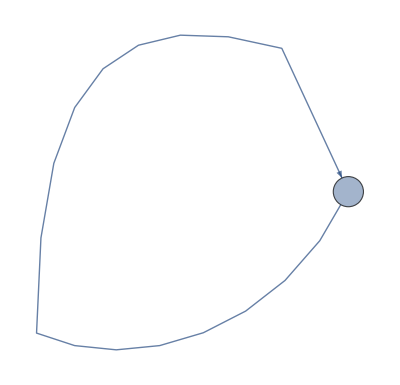
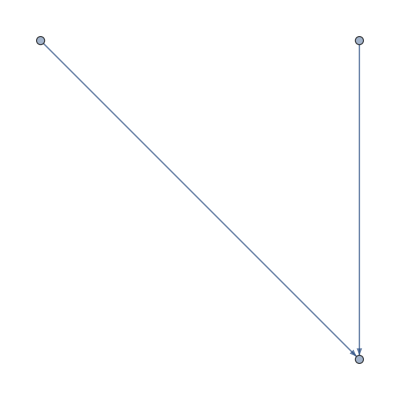
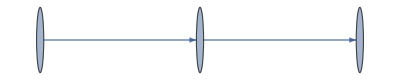
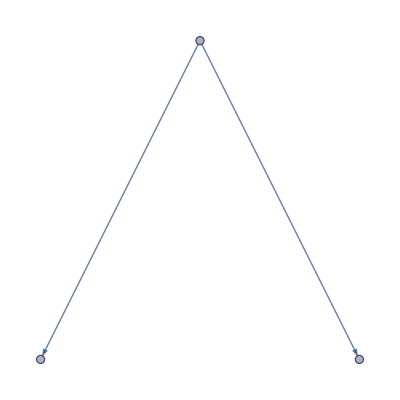
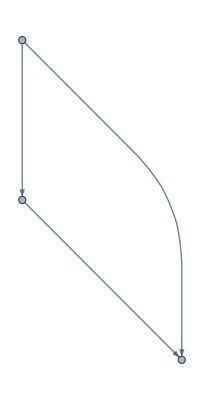

```mathematica
EnrichedCombsMFinderRandUpTo3[g_,gRands_,netMot_,pos_]:=Module[{allMotifsIns,allMotifsInsRand,ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,allregted3s,allregted3sRand,allChain3s,allChain3sRand,allIn1MFL3s,allIn1MFL3sRand,allFFL3s,allFFL3sRand,allreging3s,allreging3sRand,allRegtedMFL3s,allRegtedMFL3sRand,allOut1MFL3s,allOut1MFL3sRand,allLoopMFL3s,allLoopMFL3sRand,allRegingMFL3s,allRegingMFL3sRand,allDoubleMFL3s,allDoubleMFL3sRand,TwoMFL3SideNodes,TwoMFL3MidNodes,TwoMFL3SideNodesRand,TwoMFL3MidNodesRand,allTwoMFL3s,allTwoMFL3sRand,ThreeMFL3Nodes,ThreeMFL3NodesRand,motifsRoles,motifsRoles2,sameRoleCombs,sameRoleCombs2,nodesInMotifRoles,nodesInMotifRolesRand,motifCombs,motifCombsSame,cols,bg,t},
allMotifsIns=DeleteCases[Prepend[Table[Select[Subgraph[SimpleGraph[g],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[g]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],Select[Subgraph[g,#]&/@Union[Sort/@((Range@VertexCount[-Graphics-])/.IGLADFindSubisomorphisms[-Graphics-,g])],IsomorphicGraphQ[#,-Graphics-]&]],{}];
allMotifsInsRand=Table[Table[Select[Subgraph[SimpleGraph[gRands[[i]]],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[gRands[[i]]]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],{i,1,Length@gRands}];
ARNodes={#,1}&/@Select[EdgeList[g],#[[1]]==#[[2]]&][[;;,1]];
ARNodesRand=Table[{#,1}&/@RandomChoice[VertexList[gRands[[i]]],Length@ARNodes],{i,1,Length@gRands}];
MFL2Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
MFL2NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
allregted3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allregted3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
regted3InNodes=Tally[Flatten[#[[;;,1]]&/@(EdgeList/@(Join@@allregted3s))]];
regted3OutNodes=Tally[#[[1,2]]&/@(EdgeList/@(Join@@allregted3s))];
regted3InNodesRand=Table[Tally[Flatten[#[[;;,1]]&/@EdgeList/@(Join@@allregted3sRand[[i]])]],{i,1,Length@gRands}];
regted3OutNodesRand=Table[Tally[#[[1,2]]&/@EdgeList/@(Join@@allregted3sRand[[i]])],{i,1,Length@gRands}];
allChain3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allChain3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
chain3InNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
chain3MedNodes=Tally[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3s)];
chain3OutNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
chain3InNodesRand=Table[Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
chain3MedNodesRand=Table[Tally[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
chain3OutNodesRand=Table[Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
allIn1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allIn1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
in1MFL3InNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out1Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out2Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3InNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
in1MFL3Out1NodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
in1MFL3Out2NodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
allreging3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allreging3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
reging3InNodes=Tally[#[[1,1]]&/@(EdgeList/@(Join@@allreging3s))];
reging3OutNodes=Tally[Flatten[#[[;;,2]]&/@(EdgeList/@(Join@@allreging3s))]];
reging3InNodesRand=Table[Tally[#[[1,1]]&/@EdgeList/@(Join@@allreging3sRand[[i]])],{i,1,Length@gRands}];
reging3OutNodesRand=Table[Tally[Flatten[#[[;;,2]]&/@EdgeList/@(Join@@allreging3sRand[[i]])]],{i,1,Length@gRands}];
allFFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allFFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
FFL3InNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3MedNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3OutNodes=Tally[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3InNodesRand=Table[Tally[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
FFL3MedNodesRand=Table[Tally[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
FFL3OutNodesRand=Table[Tally[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
allRegtedMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegtedMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegtedMFL3InNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3s)];
RegtedMFL3OutNodes=Tally[Flatten[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3s)]];
RegtedMFL3InNodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3sRand[[i]])],{i,1,Length@gRands}];
RegtedMFL3OutNodesRand=Table[Tally[Flatten[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3sRand[[i]])]],{i,1,Length@gRands}];
allOut1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allOut1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
out1MFL3In1Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3In2Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3OutNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3In1NodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
out1MFL3In2NodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
out1MFL3OutNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
allTwoMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allTwoMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
TwoMFL3SideNodes=Tally[Flatten[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3s)]];
TwoMFL3MidNodes=Tally[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3s)];
TwoMFL3SideNodesRand=Table[Tally[Flatten[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]])]],{i,1,Length@gRands}];
TwoMFL3MidNodesRand=Table[Tally[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]])],{i,1,Length@gRands}];
FBL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
FBL3NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
allLoopMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allLoopMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
LoopMFL3InNodes=Tally[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3MedNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3OutNodes=Tally[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3InNodesRand=Table[Tally[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
LoopMFL3MedNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
LoopMFL3OutNodesRand=Table[Tally[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
allRegingMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegingMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegingMFL3InNodes=Tally[Flatten[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3s)]];
RegingMFL3OutNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3s)];
RegingMFL3InNodesRand=Table[Tally[Flatten[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3sRand[[i]])]],{i,1,Length@gRands}];
RegingMFL3OutNodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3sRand[[i]])],{i,1,Length@gRands}];
allDoubleMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allDoubleMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
DoubleMFL3InNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3OutNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3ConnNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3InNodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
DoubleMFL3OutNodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
DoubleMFL3ConnNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
ThreeMFL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
ThreeMFL3NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
motifsRoles={{{{a1->a1},a1}},{{{b1->b2,b2->b1},b1}},{{{y1->y2,y3->y2},y1},{{z1->z2,z3->z2},z2}},{{{g1->g2,g2->g3},g1},{{h1->h2,h2->h3},h2},{{i1->i2,i2->i3},i3}},{{{j1->j3,j2->j3,j3->j2},j1},{{k1->k3,k2->k3,k3->k2},k3},{{l1->l3,l2->l3,l3->l2},l2}},{{{t1->t2,t1->t3},t1},{{x1->x2,x1->x3},x2}},{{{c1->c2,c1->c3,c2->c3},c1},{{d1->d2,d1->d3,d2->d3},d2},{{e1->e2,e1->e3,e2->e3},e3}},{{{m1->m3,m2->m1,m2->m3,m3->m1},m2},{{n1->n3,n2->n1,n2->n3,n3->n1},n1}},{{{o2->o3,o3->o1,o3->o2},o3},{{p2->p3,p3->p1,p3->p2},p2},{{q2->q3,q3->q1,q3->q2},q1}},{{{dd1->dd2,dd2->dd1,dd2->dd3,dd3->dd2},dd1},{{ee1->ee2,ee2->ee1,ee2->ee3,ee3->ee2},ee2}},{{{f1->f2,f2->f3,f3->f1},f1}},{{{r1->r3,r2->r1,r3->r1,r3->r2},r3},{{s1->s3,s2->s1,s3->s1,s3->s2},s2},{{w1->w3,w2->w1,w3->w1,w3->w2},w1}},{{{y2->y1,y2->y3,y3->y1,y3->y2},y2},{{z2->z1,z2->z3,z3->z1,z3->z2},z1}},{{{aa1->aa3,aa2->aa1,aa2->aa3,aa3->aa1,aa3->aa2},aa2},{{bb1->bb3,bb2->bb1,bb2->bb3,bb3->bb1,bb3->bb2},bb1},{{cc1->cc3,cc2->cc1,cc2->cc3,cc3->cc1,cc3->cc2},cc3}},{{{ff1->ff2,ff2->ff1,ff2->ff3,ff3->ff2,ff3->ff1,ff1->ff3},ff1}}};
motifsRoles2=Flatten[motifsRoles[[pos]],1];
sameRoleCombs=Map[Graph[#,DirectedEdges->True]&,{{{1->1}},{{1->2,2->1,2->3,3->2}},{{1->2,3->2,3->4,5->4},{1->2,3->2,4->2,5->2}},{{1->2,2->3,1->4,4->5},{1->2,2->3,4->2,2->5},{1->2,2->3,4->5,5->3}},{{1->2,2->3,3->2,1->4,4->5,5->4},{1->2,2->3,3->2,4->2,2->5,5->2},{1->2,2->3,3->2,3->5,5->3,4->5}},{{1->2,1->3,1->4,1->5},{1->2,1->3,4->2,4->5}},{{1->2,1->3,2->3,1->4,1->5,4->5},{1->2,1->3,2->3,4->2,4->5,2->5},{1->2,1->3,2->3,4->5,4->3,5->3}},{{1->2,1->3,2->3,3->2,1->4,1->5,4->5,5->4},{1->2,1->3,2->3,3->2,5->3,5->4,3->4,4->3}},{{1->2,2->1,1->3,1->5,1->4,4->1},{1->2,2->1,2->5,1->3,3->1,3->4},{1->2,2->1,2->3,4->5,5->4,5->3}},{{1->2,2->1,2->3,3->2,1->4,4->1,4->5,5->4},{1->2,2->1,2->3,3->2,2->4,4->2,2->5,5->2}},{{1->2,2->3,3->1,1->4,4->5,5->1}},{{1->2,2->1,1->3,3->2,1->5,5->4,4->1,1->4},{1->3,3->2,2->3,2->1,1->5,5->4,4->5,4->1},{1->2,2->1,2->3,3->1,1->5,5->1,5->4,4->1}},{{1->2,2->1,1->4,2->4,2->3,3->2,2->5,3->5},{2->3,3->2,4->5,5->4,2->1,3->1,4->1,5->1}},{{1->2,2->1,2->3,3->2,1->3,1->4,4->5,5->4,1->5,5->1},{1->2,2->1,2->3,3->2,3->1,1->4,4->1,5->4,4->5,5->1},{1->2,2->1,1->5,5->1,1->3,3->1,1->4,4->1,4->5,3->2}},{{1->2,2->1,2->3,3->2,3->1,1->3,1->4,4->1,4->5,5->4,5->1,1->5}}},{2}];
sameRoleCombs2=Flatten[sameRoleCombs[[pos]],1];
nodesInMotifRoles=DeleteCases[{ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,TwoMFL3SideNodes,TwoMFL3MidNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ThreeMFL3Nodes},{}];
nodesInMotifRolesRand=Select[{ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,TwoMFL3SideNodesRand,TwoMFL3MidNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,ThreeMFL3NodesRand},Union[#]≠{{}}&]ᵀ;
motifCombs={(N@(Length[Intersection[#[[1]],#[[2]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[nodesInMotifRoles[[;;,;;,1]],{2}])/.Indeterminate->0,((N@(Length[Intersection[#[[1]],#[[2]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[#[[;;,;;,1]],{2}]&/@nodesInMotifRolesRand)ᵀ)/.Indeterminate->0,Table[Graph[(Join@@motifsRoles2[[i,1]])/.motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]],DirectedEdges->True],{i,Subsets[Range@Length[motifsRoles2],{2}]}]}ᵀ;
motifCombsSame={(N@(Count[#,_?(#[[2]]>1&)]/Length[#])&/@nodesInMotifRoles)/.Indeterminate->0,(Map[N@(Count[#,_?(#[[2]]>1&)]/Length[#])&,nodesInMotifRolesRand,{2}]ᵀ)/.Indeterminate->0,sameRoleCombs2}ᵀ;
cols=ColorData["TemperatureMap"][#]&/@Rescale[(((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(Join@@{motifCombs,motifCombsSame}))/.Indeterminate->0/.ComplexInfinity->0//Quiet)];
bg=ConstantArray[White,{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
Table[bg[[i+1,i+2;;]]=cols[[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[bg[[i+1,i+1]]=cols[[i+Length[sameRoleCombs2] (Length[sameRoleCombs2]-1)-Total[Range@(Length[sameRoleCombs2]-1)]]],{i,1,Length[sameRoleCombs2]}];
t=ConstantArray["",{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
t[[1,2;;]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&/@motifsRoles2;
Table[t[[i,1]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&@motifsRoles2[[i-1]],{i,2,Length[sameRoleCombs2]+1}];
Table[t[[i+1,i+2;;]]=Table[Graph[(Join@@motifsRoles2[[i,1]])/.motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]],DirectedEdges->True],{i,Subsets[Range@(Length[sameRoleCombs2]),{2}]}][[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[t[[i+1,i+1]]=sameRoleCombs2[[i]],{i,1,Length[sameRoleCombs2]}];
{Join@@{motifCombs,motifCombsSame},{(Join@@{motifCombs,motifCombsSame})[[#[[1]],-1]],((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(Join@@{motifCombs,motifCombsSame})[[#[[1]]]]),#[[3]]}&/@Select[{#[[1,1]],#[[1,2]],(#[[2]])/Length[(Join@@{motifCombs,motifCombsSame})] 0.05,#[[1,3]]}&/@({SortBy[Table[{i,NormalPValue[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(Join@@{motifCombs,motifCombsSame})[[i]])][[2]],(Join@@{motifCombs,motifCombsSame})[[i,1]]},{i,1,Length[(Join@@{motifCombs,motifCombsSame})]}],#[[2]]&],Range@Length[(Join@@{motifCombs,motifCombsSame})]}ᵀ),#[[2]]≤#[[3]]&&#[[4]]≥0.15&]//Quiet,BarLegend[{"TemperatureMap",{Min[#],Max[#]}&@(((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(Join@@{motifCombs,motifCombsSame}))/.Indeterminate->0/.ComplexInfinity->0//Quiet)}],Grid[t,Frame->All,Background->{None,None,Thread[Complement[Join@@Table[{i,j},{i,1,Length[sameRoleCombs2]+1},{j,1,Length[sameRoleCombs2]+1}],Position[bg,White]]->DeleteCases[Flatten[bg,1],White]]}]}
]
```

Finding significantly enriched and under-represented motif combinations of one shared node (when the random networks are already provided with autoregulation):

```mathematica
EnrichedCombsMFinderRand2UpTo3[g_,gRands_,netMot_,pos_]:=Module[{allMotifsIns,allMotifsInsRand,ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,allregted3s,allregted3sRand,allChain3s,allChain3sRand,allIn1MFL3s,allIn1MFL3sRand,allFFL3s,allFFL3sRand,allreging3s,allreging3sRand,allRegtedMFL3s,allRegtedMFL3sRand,allOut1MFL3s,allOut1MFL3sRand,allLoopMFL3s,allLoopMFL3sRand,allRegingMFL3s,allRegingMFL3sRand,allDoubleMFL3s,allDoubleMFL3sRand,TwoMFL3SideNodes,TwoMFL3MidNodes,TwoMFL3SideNodesRand,TwoMFL3MidNodesRand,allTwoMFL3s,allTwoMFL3sRand,ThreeMFL3Nodes,ThreeMFL3NodesRand,motifsRoles,motifsRoles2,sameRoleCombs,sameRoleCombs2,nodesInMotifRoles,nodesInMotifRolesRand,motifCombs,motifCombsSame,cols,bg,t},
allMotifsIns=DeleteCases[Prepend[Table[Select[Subgraph[SimpleGraph[g],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[g]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],Select[Subgraph[g,#]&/@Union[Sort/@((Range@VertexCount[-Graphics-])/.IGLADFindSubisomorphisms[-Graphics-,g])],IsomorphicGraphQ[#,-Graphics-]&]],{}];
allMotifsInsRand=Table[Table[Select[Subgraph[SimpleGraph[gRands[[i]]],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[gRands[[i]]]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],{i,1,Length@gRands}];
ARNodes={#,1}&/@Select[EdgeList[g],#[[1]]==#[[2]]&][[;;,1]];
ARNodesRand=Table[{#,1}&/@Select[EdgeList[gRands[[i]]],#[[1]]==#[[2]]&][[;;,1]],{i,1,Length@gRands}];
MFL2Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
MFL2NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
allregted3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allregted3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
regted3InNodes=Tally[Flatten[#[[;;,1]]&/@(EdgeList/@(Join@@allregted3s))]];
regted3OutNodes=Tally[#[[1,2]]&/@(EdgeList/@(Join@@allregted3s))];
regted3InNodesRand=Table[Tally[Flatten[#[[;;,1]]&/@EdgeList/@(Join@@allregted3sRand[[i]])]],{i,1,Length@gRands}];
regted3OutNodesRand=Table[Tally[#[[1,2]]&/@EdgeList/@(Join@@allregted3sRand[[i]])],{i,1,Length@gRands}];
allChain3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allChain3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
chain3InNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
chain3MedNodes=Tally[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3s)];
chain3OutNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
chain3InNodesRand=Table[Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
chain3MedNodesRand=Table[Tally[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
chain3OutNodesRand=Table[Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]])],{i,1,Length@gRands}];
allIn1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allIn1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
in1MFL3InNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out1Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out2Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3InNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
in1MFL3Out1NodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
in1MFL3Out2NodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]])],{i,1,Length@gRands}];
allreging3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allreging3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
reging3InNodes=Tally[#[[1,1]]&/@(EdgeList/@(Join@@allreging3s))];
reging3OutNodes=Tally[Flatten[#[[;;,2]]&/@(EdgeList/@(Join@@allreging3s))]];
reging3InNodesRand=Table[Tally[#[[1,1]]&/@EdgeList/@(Join@@allreging3sRand[[i]])],{i,1,Length@gRands}];
reging3OutNodesRand=Table[Tally[Flatten[#[[;;,2]]&/@EdgeList/@(Join@@allreging3sRand[[i]])]],{i,1,Length@gRands}];
allFFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allFFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
FFL3InNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3MedNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3OutNodes=Tally[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3InNodesRand=Table[Tally[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
FFL3MedNodesRand=Table[Tally[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
FFL3OutNodesRand=Table[Tally[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]]],{i,1,Length@gRands}];
allRegtedMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegtedMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegtedMFL3InNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3s)];
RegtedMFL3OutNodes=Tally[Flatten[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3s)]];
RegtedMFL3InNodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3sRand[[i]])],{i,1,Length@gRands}];
RegtedMFL3OutNodesRand=Table[Tally[Flatten[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3sRand[[i]])]],{i,1,Length@gRands}];
allOut1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allOut1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
out1MFL3In1Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3In2Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3OutNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3In1NodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
out1MFL3In2NodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
out1MFL3OutNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]])],{i,1,Length@gRands}];
allTwoMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allTwoMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
TwoMFL3SideNodes=Tally[Flatten[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3s)]];
TwoMFL3MidNodes=Tally[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3s)];
TwoMFL3SideNodesRand=Table[Tally[Flatten[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]])]],{i,1,Length@gRands}];
TwoMFL3MidNodesRand=Table[Tally[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]])],{i,1,Length@gRands}];
FBL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
FBL3NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
allLoopMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allLoopMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
LoopMFL3InNodes=Tally[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3MedNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3OutNodes=Tally[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3InNodesRand=Table[Tally[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
LoopMFL3MedNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
LoopMFL3OutNodesRand=Table[Tally[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]])],{i,1,Length@gRands}];
allRegingMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegingMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegingMFL3InNodes=Tally[Flatten[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3s)]];
RegingMFL3OutNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3s)];
RegingMFL3InNodesRand=Table[Tally[Flatten[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3sRand[[i]])]],{i,1,Length@gRands}];
RegingMFL3OutNodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3sRand[[i]])],{i,1,Length@gRands}];
allDoubleMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allDoubleMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
DoubleMFL3InNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3OutNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3ConnNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3InNodesRand=Table[Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
DoubleMFL3OutNodesRand=Table[Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
DoubleMFL3ConnNodesRand=Table[Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]])],{i,1,Length@gRands}];
ThreeMFL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
ThreeMFL3NodesRand=Table[Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
motifsRoles={{{{a1->a1},a1}},{{{b1->b2,b2->b1},b1}},{{{y1->y2,y3->y2},y1},{{z1->z2,z3->z2},z2}},{{{g1->g2,g2->g3},g1},{{h1->h2,h2->h3},h2},{{i1->i2,i2->i3},i3}},{{{j1->j3,j2->j3,j3->j2},j1},{{k1->k3,k2->k3,k3->k2},k3},{{l1->l3,l2->l3,l3->l2},l2}},{{{t1->t2,t1->t3},t1},{{x1->x2,x1->x3},x2}},{{{c1->c2,c1->c3,c2->c3},c1},{{d1->d2,d1->d3,d2->d3},d2},{{e1->e2,e1->e3,e2->e3},e3}},{{{m1->m3,m2->m1,m2->m3,m3->m1},m2},{{n1->n3,n2->n1,n2->n3,n3->n1},n1}},{{{o2->o3,o3->o1,o3->o2},o3},{{p2->p3,p3->p1,p3->p2},p2},{{q2->q3,q3->q1,q3->q2},q1}},{{{dd1->dd2,dd2->dd1,dd2->dd3,dd3->dd2},dd1},{{ee1->ee2,ee2->ee1,ee2->ee3,ee3->ee2},ee2}},{{{f1->f2,f2->f3,f3->f1},f1}},{{{r1->r3,r2->r1,r3->r1,r3->r2},r3},{{s1->s3,s2->s1,s3->s1,s3->s2},s2},{{w1->w3,w2->w1,w3->w1,w3->w2},w1}},{{{y2->y1,y2->y3,y3->y1,y3->y2},y2},{{z2->z1,z2->z3,z3->z1,z3->z2},z1}},{{{aa1->aa3,aa2->aa1,aa2->aa3,aa3->aa1,aa3->aa2},aa2},{{bb1->bb3,bb2->bb1,bb2->bb3,bb3->bb1,bb3->bb2},bb1},{{cc1->cc3,cc2->cc1,cc2->cc3,cc3->cc1,cc3->cc2},cc3}},{{{ff1->ff2,ff2->ff1,ff2->ff3,ff3->ff2,ff3->ff1,ff1->ff3},ff1}}};
motifsRoles2=Flatten[motifsRoles[[pos]],1];
sameRoleCombs=Map[Graph[#,DirectedEdges->True]&,{{{1->1}},{{1->2,2->1,2->3,3->2}},{{1->2,3->2,3->4,5->4},{1->2,3->2,4->2,5->2}},{{1->2,2->3,1->4,4->5},{1->2,2->3,4->2,2->5},{1->2,2->3,4->5,5->3}},{{1->2,2->3,3->2,1->4,4->5,5->4},{1->2,2->3,3->2,4->2,2->5,5->2},{1->2,2->3,3->2,3->5,5->3,4->5}},{{1->2,1->3,1->4,1->5},{1->2,1->3,4->2,4->5}},{{1->2,1->3,2->3,1->4,1->5,4->5},{1->2,1->3,2->3,4->2,4->5,2->5},{1->2,1->3,2->3,4->5,4->3,5->3}},{{1->2,1->3,2->3,3->2,1->4,1->5,4->5,5->4},{1->2,1->3,2->3,3->2,5->3,5->4,3->4,4->3}},{{1->2,2->1,1->3,1->5,1->4,4->1},{1->2,2->1,2->5,1->3,3->1,3->4},{1->2,2->1,2->3,4->5,5->4,5->3}},{{1->2,2->1,2->3,3->2,1->4,4->1,4->5,5->4},{1->2,2->1,2->3,3->2,2->4,4->2,2->5,5->2}},{{1->2,2->3,3->1,1->4,4->5,5->1}},{{1->2,2->1,1->3,3->2,1->5,5->4,4->1,1->4},{1->3,3->2,2->3,2->1,1->5,5->4,4->5,4->1},{1->2,2->1,2->3,3->1,1->5,5->1,5->4,4->1}},{{1->2,2->1,1->4,2->4,2->3,3->2,2->5,3->5},{2->3,3->2,4->5,5->4,2->1,3->1,4->1,5->1}},{{1->2,2->1,2->3,3->2,1->3,1->4,4->5,5->4,1->5,5->1},{1->2,2->1,2->3,3->2,3->1,1->4,4->1,5->4,4->5,5->1},{1->2,2->1,1->5,5->1,1->3,3->1,1->4,4->1,4->5,3->2}},{{1->2,2->1,2->3,3->2,3->1,1->3,1->4,4->1,4->5,5->4,5->1,1->5}}},{2}];
sameRoleCombs2=Flatten[sameRoleCombs[[pos]],1];
nodesInMotifRoles=DeleteCases[{ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,TwoMFL3SideNodes,TwoMFL3MidNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ThreeMFL3Nodes},{}];
nodesInMotifRolesRand=Select[{ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,TwoMFL3SideNodesRand,TwoMFL3MidNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,ThreeMFL3NodesRand},Union[#]≠{{}}&]ᵀ;
motifCombs={(N@(Length[Intersection[#[[1]],#[[2]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[nodesInMotifRoles[[;;,;;,1]],{2}])/.Indeterminate->0,((N@(Length[Intersection[#[[1]],#[[2]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[#[[;;,;;,1]],{2}]&/@nodesInMotifRolesRand)ᵀ)/.Indeterminate->0,Table[Graph[(Join@@motifsRoles2[[i,1]])/.motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]],DirectedEdges->True],{i,Subsets[Range@Length[motifsRoles2],{2}]}]}ᵀ;
motifCombsSame={(N@(Count[#,_?(#[[2]]>1&)]/Length[#])&/@nodesInMotifRoles)/.Indeterminate->0,(Map[N@(Count[#,_?(#[[2]]>1&)]/Length[#])&,nodesInMotifRolesRand,{2}]ᵀ)/.Indeterminate->0,sameRoleCombs2}ᵀ;
cols=ColorData["TemperatureMap"][#]&/@Rescale[(((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(Join@@{motifCombs,motifCombsSame}))/.Indeterminate->0/.ComplexInfinity->0//Quiet)];
bg=ConstantArray[White,{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
Table[bg[[i+1,i+2;;]]=cols[[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[bg[[i+1,i+1]]=cols[[i+Length[sameRoleCombs2] (Length[sameRoleCombs2]-1)-Total[Range@(Length[sameRoleCombs2]-1)]]],{i,1,Length[sameRoleCombs2]}];
t=ConstantArray["",{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
t[[1,2;;]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&/@motifsRoles2;
Table[t[[i,1]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&@motifsRoles2[[i-1]],{i,2,Length[sameRoleCombs2]+1}];
Table[t[[i+1,i+2;;]]=Table[Graph[(Join@@motifsRoles2[[i,1]])/.motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]],DirectedEdges->True],{i,Subsets[Range@(Length[sameRoleCombs2]),{2}]}][[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[t[[i+1,i+1]]=sameRoleCombs2[[i]],{i,1,Length[sameRoleCombs2]}];
{Join@@{motifCombs,motifCombsSame},{(Join@@{motifCombs,motifCombsSame})[[#[[1]],-1]],((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(Join@@{motifCombs,motifCombsSame})[[#[[1]]]]),#[[3]]}&/@Select[{#[[1,1]],#[[1,2]],(#[[2]])/Length[(Join@@{motifCombs,motifCombsSame})] 0.05,#[[1,3]]}&/@({SortBy[Table[{i,NormalPValue[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(Join@@{motifCombs,motifCombsSame})[[i]])][[2]],(Join@@{motifCombs,motifCombsSame})[[i,1]]},{i,1,Length[(Join@@{motifCombs,motifCombsSame})]}],#[[2]]&],Range@Length[(Join@@{motifCombs,motifCombsSame})]}ᵀ),#[[2]]≤#[[3]]&&#[[4]]≥0.15&]//Quiet,BarLegend[{"TemperatureMap",{Min[#],Max[#]}&@(((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(Join@@{motifCombs,motifCombsSame}))/.Indeterminate->0/.ComplexInfinity->0//Quiet)}],Grid[t,Frame->All,Background->{None,None,Thread[Complement[Join@@Table[{i,j},{i,1,Length[sameRoleCombs2]+1},{j,1,Length[sameRoleCombs2]+1}],Position[bg,White]]->DeleteCases[Flatten[bg,1],White]]}]}
]
```

```mathematica
motifRoles[g_,netMot_,pos_]:=Module[{allMotifsIns,allMotifsInsRand,ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,allregted3s,allregted3sRand,allChain3s,allChain3sRand,allIn1MFL3s,allIn1MFL3sRand,allFFL3s,allFFL3sRand,allreging3s,allreging3sRand,allRegtedMFL3s,allRegtedMFL3sRand,allOut1MFL3s,allOut1MFL3sRand,allLoopMFL3s,allLoopMFL3sRand,allRegingMFL3s,allRegingMFL3sRand,allDoubleMFL3s,allDoubleMFL3sRand,TwoMFL3SideNodes,TwoMFL3MidNodes,TwoMFL3SideNodesRand,TwoMFL3MidNodesRand,allTwoMFL3s,allTwoMFL3sRand,ThreeMFL3Nodes,ThreeMFL3NodesRand,motifsRoles,motifsRoles2,sameRoleCombs,sameRoleCombs2,nodesInMotifRoles,nodesInMotifRolesRand,motifCombs,motifCombsSame,cols,bg,t},
allMotifsIns=DeleteCases[Prepend[Table[Select[Subgraph[SimpleGraph[g],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[g]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],Select[Subgraph[g,#]&/@Union[Sort/@((Range@VertexCount[-Graphics-])/.IGLADFindSubisomorphisms[-Graphics-,g])],IsomorphicGraphQ[#,-Graphics-]&]],{}];
ARNodes={#,1}&/@Select[EdgeList[g],#[[1]]==#[[2]]&][[;;,1]];
MFL2Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allregted3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
regted3InNodes=Tally[Flatten[#[[;;,1]]&/@(EdgeList/@(Join@@allregted3s))]];
regted3OutNodes=Tally[#[[1,2]]&/@(EdgeList/@(Join@@allregted3s))];
allChain3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
chain3InNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
chain3MedNodes=Tally[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3s)];
chain3OutNodes=Tally[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3s)];
allIn1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
in1MFL3InNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out1Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3s)];
in1MFL3Out2Nodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s)];
allreging3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
reging3InNodes=Tally[#[[1,1]]&/@(EdgeList/@(Join@@allreging3s))];
reging3OutNodes=Tally[Flatten[#[[;;,2]]&/@(EdgeList/@(Join@@allreging3s))]];
allFFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
FFL3InNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3MedNodes=Tally[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
FFL3OutNodes=Tally[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]]];
allRegtedMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
RegtedMFL3InNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3s)];
RegtedMFL3OutNodes=Tally[Flatten[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3s)]];
allOut1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
out1MFL3In1Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3In2Nodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
out1MFL3OutNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s)];
allTwoMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
TwoMFL3SideNodes=Tally[Flatten[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3s)]];
TwoMFL3MidNodes=Tally[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3s)];
FBL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allLoopMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
LoopMFL3InNodes=Tally[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3MedNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
LoopMFL3OutNodes=Tally[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s)];
allRegingMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
RegingMFL3InNodes=Tally[Flatten[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3s)]];
RegingMFL3OutNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3s)];
allDoubleMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
DoubleMFL3InNodes=Tally[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3OutNodes=Tally[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s)];
DoubleMFL3ConnNodes=Tally[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3s)];
ThreeMFL3Nodes=Tally[Flatten[VertexList/@Flatten[#]]]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
nodesInMotifRoles=DeleteCases[{{"ARNodes","MFL2Nodes","regted3InNodes","regted3OutNodes","chain3InNodes","chain3MedNodes","chain3OutNodes","in1MFL3InNodes","in1MFL3Out1Nodes","in1MFL3Out2Nodes","reging3InNodes","reging3OutNodes","FFL3InNodes","FFL3MedNodes","FFL3OutNodes","RegtedMFL3InNodes","RegtedMFL3OutNodes","out1MFL3In1Nodes","out1MFL3In2Nodes","out1MFL3OutNodes","TwoMFL3SideNodes","TwoMFL3MidNodes","FBL3Nodes","LoopMFL3InNodes","LoopMFL3MedNodes","LoopMFL3OutNodes","RegingMFL3InNodes","RegingMFL3OutNodes","DoubleMFL3InNodes","DoubleMFL3OutNodes","DoubleMFL3ConnNodes","ThreeMFL3Nodes"},{ARNodes,MFL2Nodes,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,TwoMFL3SideNodes,TwoMFL3MidNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ThreeMFL3Nodes}}ᵀ,{_,{}}];
nodesInMotifRoles
]
```

```mathematica
IsSubG[g_,sg_]:=Module[{subs},
subs=Select[Gather[(Subgraph[g,#]&/@Union[(Sort/@(Range[VertexCount[sg]]/.IGLADFindSubisomorphisms[AdjacencyGraph[AdjacencyMatrix[sg],DirectedEdges->True],g]))]),IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[#[[1]],AdjacencyGraph[AdjacencyMatrix[sg],DirectedEdges->True]]&];
subs≠{}]
```

```mathematica
NumSubG[g_,sg_]:=Module[{subs},
subs=Length[Join@@Select[Gather[(Subgraph[g,#]&/@Union[(Sort/@(Range[VertexCount[sg]]/.IGLADFindSubisomorphisms[AdjacencyGraph[AdjacencyMatrix[sg],DirectedEdges->True],g]))]),IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[#[[1]],AdjacencyGraph[AdjacencyMatrix[sg],DirectedEdges->True]]&]];
subs]
```

```mathematica
AllSubG[g_,sg_]:=Module[{subs},
subs=Select[Gather[(Subgraph[g,#]&/@Union[(Sort/@(Range[VertexCount[sg]]/.IGLADFindSubisomorphisms[AdjacencyGraph[AdjacencyMatrix[sg],DirectedEdges->True],g]))]),IsomorphicGraphQ[#1,#2]&],IsomorphicGraphQ[#[[1]],AdjacencyGraph[AdjacencyMatrix[sg],DirectedEdges->True]]&];
subs]
```

Finding significantly enriched motif combinations of two shared nodes:

```mathematica
EnrichedCombs2ShMFinderRandUpTo3[g_,gRands_,netMot_,pos_]:=Module[{allMotifsIns,allMotifsInsRand,regted3InNodes,regted3OutNodes,chain3InNodes,chain3MedNodes,chain3OutNodes,in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes,reging3InNodes,reging3OutNodes,FFL3InNodes,FFL3MedNodes,FFL3OutNodes,RegtedMFL3InNodes,RegtedMFL3OutNodes,out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes,FBL3Nodes,LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes,RegingMFL3InNodes,RegingMFL3OutNodes,DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes,ARNodesRand,MFL2NodesRand,regted3InNodesRand,regted3OutNodesRand,chain3InNodesRand,chain3MedNodesRand,chain3OutNodesRand,in1MFL3InNodesRand,in1MFL3Out1NodesRand,in1MFL3Out2NodesRand,reging3InNodesRand,reging3OutNodesRand,FFL3InNodesRand,FFL3MedNodesRand,FFL3OutNodesRand,RegtedMFL3InNodesRand,RegtedMFL3OutNodesRand,out1MFL3In1NodesRand,out1MFL3In2NodesRand,out1MFL3OutNodesRand,FBL3NodesRand,LoopMFL3InNodesRand,LoopMFL3MedNodesRand,LoopMFL3OutNodesRand,RegingMFL3InNodesRand,RegingMFL3OutNodesRand,DoubleMFL3InNodesRand,DoubleMFL3OutNodesRand,DoubleMFL3ConnNodesRand,regted3PairRolesRand,chain3PairRolesRand,in1MFL3PairRolesRand,reging3PairRolesRand,fflPairRolesRand,RegtedMFL3PairRolesRand,out1MFL3PairRolesRand,FBL3PairRolesRand,LoopMFL3PairRolesRand,RegingMFL3PairRolesRand,DoubleMFL3PairRolesRand,allregted3s,allregted3sRand,allChain3s,allChain3sRand,allIn1MFL3s,allIn1MFL3sRand,allFFL3s,allFFL3sRand,allreging3s,allreging3sRand,allRegtedMFL3s,allRegtedMFL3sRand,allOut1MFL3s,allOut1MFL3sRand,allLoopMFL3s,allLoopMFL3sRand,allRegingMFL3s,allRegingMFL3sRand,allDoubleMFL3s,allDoubleMFL3sRand,motifsRoles,regted3PairRoles,chain3PairRoles,in1MFL3PairRoles,reging3PairRoles,fflPairRoles,RegtedMFL3PairRoles,out1MFL3PairRoles,FBL3PairRoles,LoopMFL3PairRoles,RegingMFL3PairRoles,DoubleMFL3PairRoles,allTwoMFL3s,allTwoMFL3sRand,TwoMFL3SideNodes,TwoMFL3SideNodesRand,TwoMFL3MidNodes,TwoMFL3MidNodesRand,TwoMFL3PairRoles,TwoMFL3PairRolesRand,ThreeMFL3Nodes,ThreeMFL3NodesRand,ThreeMFL3PairRoles,ThreeMFL3PairRolesRand,motifCombs2,motifsRoles2,sameRoleCombs,sameRoleCombs2,motifCombs,motifCombsSame,nodesInMotifRoles,nodesInMotifRolesRand,cols,bg,t},
allMotifsIns=DeleteCases[Prepend[Table[Select[Subgraph[SimpleGraph[g],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[g]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],Select[Subgraph[g,#]&/@Union[Sort/@((Range@VertexCount[-Graphics-])/.IGLADFindSubisomorphisms[-Graphics-,g])],IsomorphicGraphQ[#,-Graphics-]&]],{}];
allMotifsInsRand=Table[Table[Select[Subgraph[SimpleGraph[gRands[[i]]],#]&/@Union[Sort/@((Range@VertexCount[motif])/.IGLADFindSubisomorphisms[motif,SimpleGraph[gRands[[i]]]])],IsomorphicGraphQ[SimpleGraph[#],motif]&],{motif,Select[netMot,-Graphics-≠ #&]}],{i,1,Length@gRands}];
allregted3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allregted3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
regted3InNodes=#[[;;,1]]&/@(EdgeList/@(Join@@allregted3s));
regted3OutNodes=#[[1,2]]&/@(EdgeList/@(Join@@allregted3s));
regted3InNodesRand=Table[#[[;;,1]]&/@EdgeList/@(Join@@allregted3sRand[[i]]),{i,1,Length@gRands}];
regted3OutNodesRand=Table[#[[1,2]]&/@EdgeList/@(Join@@allregted3sRand[[i]]),{i,1,Length@gRands}];
regted3PairRoles={Join@@({{#[[2]],#[[1,1]]},{#[[2]],#[[1,2]]}}&/@({regted3InNodes,regted3OutNodes}ᵀ)),regted3InNodes};
regted3PairRolesRand=Table[{Join@@({{#[[2]],#[[1,1]]},{#[[2]],#[[1,2]]}}&/@({regted3InNodesRand[[i]],regted3OutNodesRand[[i]]}ᵀ)),regted3InNodesRand[[i]]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
allChain3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allChain3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
chain3InNodes=Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3s);
chain3MedNodes=Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3s);
chain3OutNodes=Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3s);
chain3InNodesRand=Table[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,2]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]]),{i,1,Length@gRands}];
chain3MedNodesRand=Table[Select[Tally[Flatten[{#[[;;,1]],#[[;;,2]]},1]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allChain3sRand[[i]]),{i,1,Length@gRands}];
chain3OutNodesRand=Table[Complement[Flatten[{#[[;;,1]],#[[;;,2]]},1],#[[;;,1]]][[1]]&/@EdgeList/@(Join@@allChain3sRand[[i]]),{i,1,Length@gRands}];
chain3PairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({chain3InNodes,chain3MedNodes,chain3OutNodes}ᵀ))ᵀ;
chain3PairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({chain3InNodesRand[[i]],chain3MedNodesRand[[i]],chain3OutNodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
allIn1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allIn1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
in1MFL3InNodes=Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s);
in1MFL3Out1Nodes=Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3s);
in1MFL3Out2Nodes=Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3s);
in1MFL3InNodesRand=Table[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]]),{i,1,Length@gRands}];
in1MFL3Out1NodesRand=Table[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]]),{i,1,Length@gRands}];
in1MFL3Out2NodesRand=Table[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allIn1MFL3sRand[[i]]),{i,1,Length@gRands}];
in1MFL3PairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({in1MFL3InNodes,in1MFL3Out1Nodes,in1MFL3Out2Nodes}ᵀ))ᵀ;
in1MFL3PairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({in1MFL3InNodesRand[[i]],in1MFL3Out1NodesRand[[i]],in1MFL3Out2NodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
allreging3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allreging3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
reging3InNodes=#[[1,1]]&/@(EdgeList/@(Join@@allreging3s));
reging3OutNodes=#[[;;,2]]&/@(EdgeList/@(Join@@allreging3s));
reging3InNodesRand=Table[#[[1,1]]&/@EdgeList/@(Join@@allreging3sRand[[i]]),{i,1,Length@gRands}];
reging3OutNodesRand=Table[#[[;;,2]]&/@EdgeList/@(Join@@allreging3sRand[[i]]),{i,1,Length@gRands}];
reging3PairRoles={Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({reging3InNodes,reging3OutNodes}ᵀ)),reging3OutNodes};
reging3PairRolesRand=Table[{Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({reging3InNodesRand[[i]],reging3OutNodesRand[[i]]}ᵀ)),reging3OutNodesRand[[i]]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
allFFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allFFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
FFL3InNodes=(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]];
FFL3MedNodes=(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]];
FFL3OutNodes=(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3s)))[[;;,1]];
FFL3InNodesRand=Table[(Select[Tally[#[[;;,1]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]],{i,1,Length@gRands}];
FFL3MedNodesRand=Table[(Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]],{i,1,Length@gRands}];
FFL3OutNodesRand=Table[(Select[Tally[#[[;;,2]]],#[[2]]==2&][[;;,1]]&/@(EdgeList/@(Join@@allFFL3sRand[[i]])))[[;;,1]],{i,1,Length@gRands}];
fflPairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({FFL3InNodes,FFL3MedNodes,FFL3OutNodes}ᵀ))ᵀ;
fflPairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({FFL3InNodesRand[[i]],FFL3MedNodesRand[[i]],FFL3OutNodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
allRegtedMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegtedMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegtedMFL3InNodes=Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3s);
RegtedMFL3OutNodes=Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3s);
RegtedMFL3InNodesRand=Table[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegtedMFL3sRand[[i]]),{i,1,Length@gRands}];
RegtedMFL3OutNodesRand=Table[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegtedMFL3sRand[[i]]),{i,1,Length@gRands}];
RegtedMFL3PairRoles={Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({RegtedMFL3InNodes,RegtedMFL3OutNodes}ᵀ)),RegtedMFL3OutNodes};
RegtedMFL3PairRolesRand=Table[{Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({RegtedMFL3InNodesRand[[i]],RegtedMFL3OutNodesRand[[i]]}ᵀ)),RegtedMFL3OutNodesRand[[i]]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
allOut1MFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allOut1MFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
out1MFL3In1Nodes=Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3s);
out1MFL3In2Nodes=Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s);
out1MFL3OutNodes=Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3s);
out1MFL3In1NodesRand=Table[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]]),{i,1,Length@gRands}];
out1MFL3In2NodesRand=Table[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]]),{i,1,Length@gRands}];
out1MFL3OutNodesRand=Table[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==1&][[1,1]]&/@(Join@@allOut1MFL3sRand[[i]]),{i,1,Length@gRands}];
out1MFL3PairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({out1MFL3In1Nodes,out1MFL3In2Nodes,out1MFL3OutNodes}ᵀ))ᵀ;
out1MFL3PairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({out1MFL3In1NodesRand[[i]],out1MFL3In2NodesRand[[i]],out1MFL3OutNodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
allTwoMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allTwoMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
TwoMFL3SideNodes=Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3s);
TwoMFL3MidNodes=Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3s);
TwoMFL3SideNodesRand=Table[Select[Tally[#[[;;,1]]],#[[2]]==1&][[;;,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]]),{i,1,Length@gRands}];
TwoMFL3MidNodesRand=Table[Select[Tally[#[[;;,1]]],#[[2]]==2&][[1,1]]&/@EdgeList/@(Join@@allTwoMFL3sRand[[i]]),{i,1,Length@gRands}];
TwoMFL3PairRoles={Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({TwoMFL3MidNodes,TwoMFL3SideNodes}ᵀ)),TwoMFL3SideNodes};
TwoMFL3PairRolesRand=Table[{Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({TwoMFL3MidNodesRand[[i]],TwoMFL3SideNodesRand[[i]]}ᵀ)),TwoMFL3SideNodesRand[[i]]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
FBL3Nodes=VertexList/@Flatten[#]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
FBL3NodesRand=Table[VertexList/@Flatten[#]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
FBL3PairRoles={Flatten[Subsets[#,{2}]&/@FBL3Nodes,1]};
FBL3PairRolesRand=Table[{Flatten[Subsets[#,{2}]&/@FBL3NodesRand[[i]],1]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
allLoopMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allLoopMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
LoopMFL3InNodes=Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s);
LoopMFL3MedNodes=Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s);
LoopMFL3OutNodes=Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3s);
LoopMFL3InNodesRand=Table[Select[Tally[(#[[1]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]]),{i,1,Length@gRands}];
LoopMFL3MedNodesRand=Table[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]]),{i,1,Length@gRands}];
LoopMFL3OutNodesRand=Table[Select[Tally[(#[[2]]&/@EdgeList[#])],#[[2]]==2&][[1,1]]&/@(Join@@allLoopMFL3sRand[[i]]),{i,1,Length@gRands}];
LoopMFL3PairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({LoopMFL3InNodes,LoopMFL3MedNodes,LoopMFL3OutNodes}ᵀ))ᵀ;
LoopMFL3PairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({LoopMFL3InNodesRand[[i]],LoopMFL3MedNodesRand[[i]],LoopMFL3OutNodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
allRegingMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allRegingMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
RegingMFL3InNodes=Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3s);
RegingMFL3OutNodes=Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3s);
RegingMFL3InNodesRand=Table[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[;;,1]]&/@(Join@@allRegingMFL3sRand[[i]]),{i,1,Length@gRands}];
RegingMFL3OutNodesRand=Table[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==2&][[1,1]]&/@(Join@@allRegingMFL3sRand[[i]]),{i,1,Length@gRands}];
RegingMFL3PairRoles={Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({RegingMFL3OutNodes,RegingMFL3InNodes}ᵀ)),RegingMFL3InNodes};
RegingMFL3PairRolesRand=Table[{Join@@({{#[[1]],#[[2,1]]},{#[[1]],#[[2,2]]}}&/@({RegingMFL3OutNodesRand[[i]],RegingMFL3InNodesRand[[i]]}ᵀ)),RegingMFL3InNodesRand[[i]]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
allDoubleMFL3s=Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
allDoubleMFL3sRand=Table[Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
DoubleMFL3InNodes=Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s);
DoubleMFL3OutNodes=Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3s);
DoubleMFL3ConnNodes=Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3s);
DoubleMFL3InNodesRand=Table[Select[Tally[#[[2]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]]),{i,1,Length@gRands}];
DoubleMFL3OutNodesRand=Table[Select[Tally[#[[1]]&/@EdgeList[#]],#[[2]]==1&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]]),{i,1,Length@gRands}];
DoubleMFL3ConnNodesRand=Table[Select[Tally[Join@@({#[[1]],#[[2]]}&/@EdgeList[#])],#[[2]]==4&][[1,1]]&/@(Join@@allDoubleMFL3sRand[[i]]),{i,1,Length@gRands}];
DoubleMFL3PairRoles=({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({DoubleMFL3InNodes,DoubleMFL3OutNodes,DoubleMFL3ConnNodes}ᵀ))ᵀ;
DoubleMFL3PairRolesRand=Table[({#[[{1,2}]],#[[{1,3}]],#[[{2,3}]]}&/@({DoubleMFL3InNodesRand[[i]],DoubleMFL3OutNodesRand[[i]],DoubleMFL3ConnNodesRand[[i]]}ᵀ))ᵀ,{i,1,Length@gRands}]/.(Transpose[{}]->{});
ThreeMFL3Nodes=VertexList/@Flatten[#]&@Select[allMotifsIns,IsomorphicGraphQ[#[[1]],-Graphics-]&];
ThreeMFL3NodesRand=Table[VertexList/@Flatten[#]&@Select[allMotifsInsRand[[i]],IsomorphicGraphQ[#[[1]],-Graphics-]&],{i,1,Length@gRands}];
ThreeMFL3PairRoles={Flatten[Subsets[#,{2}]&/@ThreeMFL3Nodes,1]};
ThreeMFL3PairRolesRand=Table[{Flatten[Subsets[#,{2}]&/@ThreeMFL3NodesRand[[i]],1]},{i,1,Length@gRands}]/.(Transpose[{}]->{});
motifsRoles={{},{},{{{y1->y2,y3->y2},{y1,y2}},{{z1->z2,z3->z2},{z1,z3}}},{{{g1->g2,g2->g3},{g1,g2}},{{h1->h2,h2->h3},{h1,h3}},{{i1->i2,i2->i3},{i2,i3}}},{{{j1->j3,j2->j3,j3->j2},{j1,j3}},{{k1->k3,k2->k3,k3->k2},{k1,k2}},{{l1->l3,l2->l3,l3->l2},{l3,l2}}},{{{t1->t2,t1->t3},{t1,t2}},{{x1->x2,x1->x3},{x2,x3}}},{{{c1->c2,c1->c3,c2->c3},{c1,c2}},{{d1->d2,d1->d3,d2->d3},{d1,d3}},{{e1->e2,e1->e3,e2->e3},{e2,e3}}},{{{m1->m3,m2->m1,m2->m3,m3->m1},{m2,m1}},{{n1->n3,n2->n1,n2->n3,n3->n1},{n1,n3}}},{{{o2->o3,o3->o1,o3->o2},{o3,o2}},{{p2->p3,p3->p1,p3->p2},{p3,p1}},{{q2->q3,q3->q1,q3->q2},{q2,q1}}},{{{dd1->dd2,dd2->dd1,dd2->dd3,dd3->dd2},{dd1,dd2}},{{ee1->ee2,ee2->ee1,ee2->ee3,ee3->ee2},{ee1,ee3}}},{{{f1->f2,f2->f3,f3->f1},{f1,f2}}},{{{r1->r3,r2->r1,r3->r1,r3->r2},{r3,r2}},{{s1->s3,s2->s1,s3->s1,s3->s2},{s3,s1}},{{w1->w3,w2->w1,w3->w1,w3->w2},{w2,w1}}},{{{y2->y1,y2->y3,y3->y1,y3->y2},{y2,y1}},{{z2->z1,z2->z3,z3->z1,z3->z2},{z2,z3}}},{{{aa1->aa3,aa2->aa1,aa2->aa3,aa3->aa1,aa3->aa2},{aa2,aa1}},{{bb1->bb3,bb2->bb1,bb2->bb3,bb3->bb1,bb3->bb2},{bb2,bb3}},{{cc1->cc3,cc2->cc1,cc2->cc3,cc3->cc1,cc3->cc2},{cc1,cc3}}},{{{ff1->ff2,ff2->ff1,ff2->ff3,ff3->ff2,ff3->ff1,ff1->ff3},{ff1,ff2}}}};
motifsRoles2=Flatten[motifsRoles[[pos]],1];
sameRoleCombs=Map[Graph[#,DirectedEdges->True]&,{{{}},{{}},{{1->2,3->2,5->2},{1->2,1->3,4->2,4->3}},{{1->2,2->3,2->4},{1->2,2->3,1->4,4->3},{1->2,2->3,4->2}},{{1->2,2->3,3->2,2->4,4->2},{1->2,2->3,3->2,1->4,4->3,3->4},{1->2,2->3,3->2,4->2}},{{1->2,1->3,1->4},{1->2,1->3,4->2,4->3}},{{1->2,1->3,2->3,1->4,2->4},{1->2,2->3,1->3,1->4,4->3},{1->2,2->3,1->3,4->2,4->3}},{{1->2,1->3,2->3,3->2,1->4,2->4,4->2},{1->2,1->3,2->3,3->2,4->2,4->3}},{{1->2,2->1,1->3,1->4},{1->2,2->1,1->3,1->4,4->1},{1->2,2->1,1->3,2->4,4->2,4->3}},{{1->2,2->1,2->3,3->2,2->4,4->2},{1->2,2->1,2->3,3->2,1->4,4->1,3->4,4->3}},{{1->2,2->3,3->1,2->4,4->1}},{{1->2,2->1,1->3,3->2,3->4,4->1,1->4},{1->2,2->1,1->3,3->2,1->4,4->2},{1->2,2->1,1->3,3->2,2->4,4->2,4->3}},{{1->2,2->1,1->3,2->3,1->4,4->1,4->3},{1->2,2->1,1->3,2->3,1->4,2->4}},{{1->2,2->1,2->3,3->2,1->3,1->4,4->1,3->4,4->3},{1->2,2->1,2->3,3->2,1->3,1->4,4->2,2->4},{1->2,2->1,2->3,3->2,1->3,2->4,4->2,4->3}},{{1->2,2->1,2->3,3->2,3->1,1->3,2->4,4->2,3->4,4->3}}},{2}];
sameRoleCombs2=Flatten[sameRoleCombs[[pos]],1];
nodesInMotifRoles=Flatten[DeleteCases[{{},{},regted3PairRoles,chain3PairRoles,in1MFL3PairRoles,reging3PairRoles,fflPairRoles,RegtedMFL3PairRoles,out1MFL3PairRoles,TwoMFL3PairRoles,FBL3PairRoles,LoopMFL3PairRoles,RegingMFL3PairRoles,DoubleMFL3PairRoles,ThreeMFL3PairRoles}[[pos]],{}],1];
nodesInMotifRolesRand=Flatten[#,1]&/@(DeleteCases[{{},{},regted3PairRolesRand,chain3PairRolesRand,in1MFL3PairRolesRand,reging3PairRolesRand,fflPairRolesRand,RegtedMFL3PairRolesRand,out1MFL3PairRolesRand,TwoMFL3PairRolesRand,FBL3PairRolesRand,LoopMFL3PairRolesRand,RegingMFL3PairRolesRand,DoubleMFL3PairRolesRand,ThreeMFL3PairRolesRand}[[pos]],{}]ᵀ);
motifCombs={(N@(Length[Intersection[Union[#[[1]]],Union[#[[2]]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[Map[Sort[#]&,nodesInMotifRoles,{2}],{2}])/.Indeterminate->0,(((N@(Length[Intersection[#[[1]],#[[2]]]]/Length[Union[#[[1]],#[[2]]]])&/@Subsets[Map[Sort[#]&,#,{2}],{2}])&/@Select[nodesInMotifRolesRand,Dimensions[#][[1]]==Dimensions[nodesInMotifRoles][[1]]&])ᵀ)/.Indeterminate->0,Table[If[(NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[1]],1]]]]≥1&&NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[2]],1]]]]≥1&&!IsomorphicGraphQ[Graph[motifsRoles2[[i[[1]],1]]],Graph[motifsRoles2[[i[[2]],1]]]])||(NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[1]],1]]]]≥2&&IsomorphicGraphQ[Graph[motifsRoles2[[i[[1]],1]]],Graph[motifsRoles2[[i[[2]],1]]]]),Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],{}],{i,Subsets[Range@(Length[motifsRoles2]),{2}]}]}ᵀ;
motifCombsSame={(N@(Count[#,_?(#[[2]]>1&)]/Length[#])&/@(Tally/@Map[Sort[#]&,nodesInMotifRoles,{2}]))/.Indeterminate->0,((N@(Count[#,_?(#[[2]]>1&)]/Length[#])&/@(Tally/@Map[Sort[#]&,#,{2}]))&/@Select[nodesInMotifRolesRand,Dimensions[#][[1]]==Dimensions[nodesInMotifRoles][[1]]&])ᵀ/.Indeterminate->0,sameRoleCombs2}ᵀ;
cols=ColorData["TemperatureMap"][#]&/@Rescale[(((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(Join@@{motifCombs,motifCombsSame}))/.Indeterminate->0/.ComplexInfinity->0//Quiet)];
bg=ConstantArray[White,{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
Table[bg[[i+1,i+2;;]]=cols[[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[bg[[i+1,i+1]]=cols[[i+Length[sameRoleCombs2] (Length[sameRoleCombs2]-1)-Total[Range@(Length[sameRoleCombs2]-1)]]],{i,1,Length[sameRoleCombs2]}];
t=ConstantArray["",{Length[sameRoleCombs2]+1,Length[sameRoleCombs2]+1}];
t[[1,2;;]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&/@motifsRoles2;
Table[t[[i,1]]=HighlightGraph[#[[1]],#[[2]],VertexSize->0.07]&@motifsRoles2[[i-1]],{i,2,Length[sameRoleCombs2]+1}];
Table[t[[i+1,i+2;;]]=Table[If[(NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[1]],1]]]]≥1&&NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[2]],1]]]]≥1&&!IsomorphicGraphQ[Graph[motifsRoles2[[i[[1]],1]]],Graph[motifsRoles2[[i[[2]],1]]]])||(NumSubG[Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],Graph[motifsRoles2[[i[[1]],1]]]]≥2&&IsomorphicGraphQ[Graph[motifsRoles2[[i[[1]],1]]],Graph[motifsRoles2[[i[[2]],1]]]]),Graph[Union[(Join@@motifsRoles2[[i,1]])/.Thread[motifsRoles2[[i[[1]],2]]->motifsRoles2[[i[[2]],2]]]],DirectedEdges->True],{}],{i,Subsets[Range@(Length[motifsRoles2]),{2}]}][[Length[sameRoleCombs2] i-Total[Range@i]-(Length[sameRoleCombs2]-1-i);;Length[sameRoleCombs2] i-Total[Range@i]]],{i,1,Length[sameRoleCombs2]-1}];
Table[t[[i+1,i+1]]=sameRoleCombs2[[i]],{i,1,Length[sameRoleCombs2]}];
motifCombs2=DeleteCases[Join@@{motifCombs,motifCombsSame},{_,_,{}}];
{motifCombs2,{(motifCombs2)[[#[[1]],-1]],((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(motifCombs2)[[#[[1]]]]),#[[3]]}&/@Select[{#[[1,1]],#[[1,2]],(#[[2]])/Length[(motifCombs2)] 0.05,#[[1,3]]}&/@({SortBy[Table[{i,NormalPValue[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&@(motifCombs2)[[i]])][[2]],(motifCombs2)[[i,1]]},{i,1,Length[(motifCombs2)]}],#[[2]]&],Range@Length[(motifCombs2)]}ᵀ),#[[2]]≤#[[3]]&]//Quiet,BarLegend[{"TemperatureMap",{Min[#],Max[#]}&@(((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@(motifCombs2))/.Indeterminate->0/.ComplexInfinity->0//Quiet)}],Grid[t,Frame->All,Background->{None,None,Thread[Complement[Join@@Table[{i,j},{i,1,Length[sameRoleCombs2]+1},{j,1,Length[sameRoleCombs2]+1}],Position[bg,White]]->DeleteCases[Flatten[bg,1],White]]}]}
]
```

## Generating synthetic networks

```mathematica
g=Graph[Join[Join@@Table[{x->y,y->z,x->z}/.Thread[{x,y,z}->Range[i-2,i]],{i,Table[3x,{x,1,20}]}]]];
```

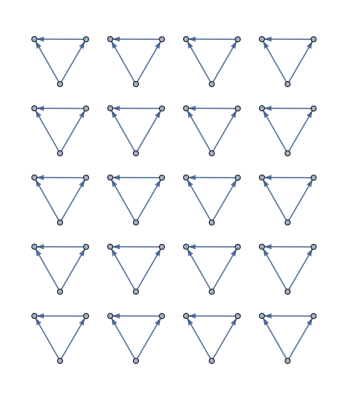

```mathematica
g
```

Synthetic network #2:

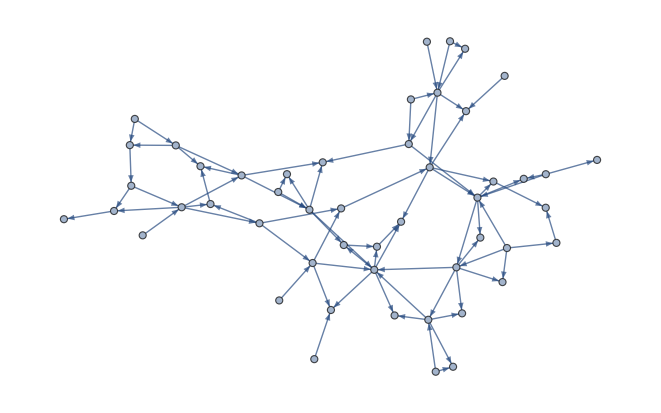

```mathematica
g2=Graph[Union[Join[EdgeList[g]/.(#[[1,2]]->#[[2,1]]&/@(RandomSample[(Subsets[Range[#-2,#]&/@Table[3x,{x,1,20}],{2}]),120])),
RandomChoice[#[[1]]]->RandomChoice[#[[2]]]&/@(RandomSample[(Subsets[Range[#-2,#]&/@Table[3x,{x,1,20}],{2}]),20])]]];
```

Import the first synthetic network:

```mathematica
g2=Graph[DirectedEdge@@@Import["/synt1.txt","Table"][[;;,;;2]],EdgeStyle->Black,VertexSize->Tiny];
```

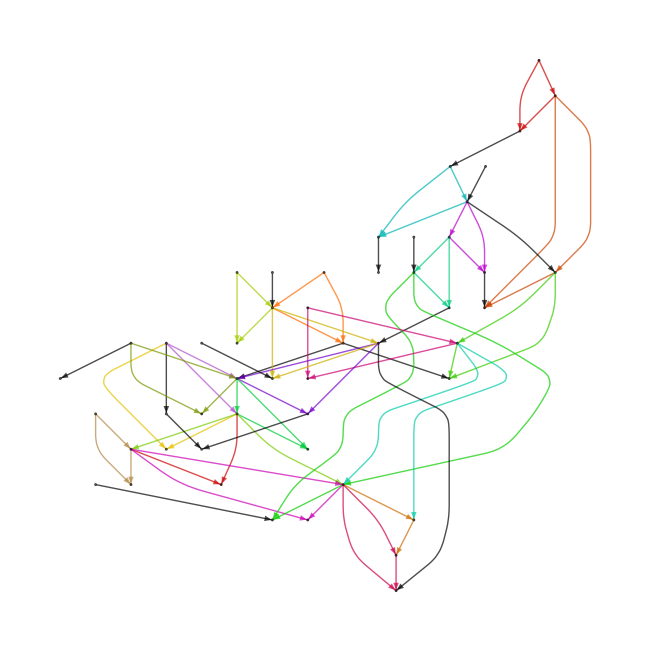

```mathematica
HighlightGraph[g2,AllSubG[g2,Graph[{1->2,2->3,1->3}]][[1]],GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
EdgeCount[g2]
```

80

```mathematica
VertexCount[g2]
```

50

Detecting network motifs with mathematica:

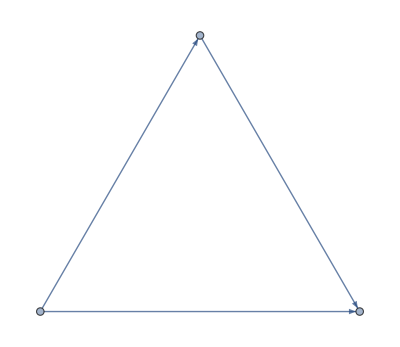
{{},{},{{-Graphics-,23,11.7759}}}

```mathematica
NetMotFinderAllUp3[g2,1]
```

Detecting network motifs with mFinder:

```mathematica
SyntMFinder3N=Import["/synt1_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression/@StringSplit/@SyntMFinder3N[[38;;40]][[;;,1]]]
```

-Graphics-

```mathematica
SyntMFinder3N//TableForm
```

| 
Summary motif results | 
===================== | 
mfinder Version 1.20 | 
 | 
MOTIF FINDER RESULTS: | 
 | 
Network name: synt1.txt | 
Network type: Directed | 
Num of Nodes: 60 Num of Edges: 140 | 
Num of Nodes with edges: 55 | 
Maximal out degree (out-hub) : 12 | 
Maximal in degree (in-hub) : 10 | 
Roots num: 5 Leaves num: 17 | 
Single Edges num: 138 Mutual Edges num: 1 | 
 | 
Motif size searched  3 | 
Total number of 3-node subgraphs : 720 | 
Number of random networks generated : 100 | 
Random networks generation method: Switches | 
Num of Switches range: 100.0-200.0 | Success switches Ratio:0.674+-0.00
 | 
The following motifs were found: | 
 | 
Criteria taken : Nreal Zscore > 2.00 | 
Pval ignored (due to small number of random networks) | 
Mfactor > 1.10 | 
Uniqueness >= 4 | 
 | 
 | 
 | 
Full list includes 1 motifs | 
MOTIF	NREAL	NRAND		NREAL	NREAL	UNIQ	CREAL | 
ID		STATS		ZSCORE	PVAL	VAL	[MILI] | 
 | 
38	44	27.5+-4.2	3.94	0.000	11	61.11 | 
 | 
0 1 1 | 
0 0 1 | 
0 0 0 | 
 | 
 | 
 | 
 | 
Full list of subgraphs size 3 ids: | 
 | 
( Total num of different subgraphs size 3 is : 13 ) | 
 | 
MOTIF	NREAL	NRAND		NREAL	NREAL	CREAL	UNIQ | 
ID		STATS		ZSCORE	PVAL	[MILI] | 
6	257	273.5+-4.2	-3.94	1.000	356.94	14 | 
 | 
12	233	243.3+-6.4	-1.62	0.930	323.61	11 | 
 | 
14	9	12.1+-1.4	-2.23	1.000	12.50	1 | 
 | 
36	167	184.8+-4.3	-4.11	1.000	231.94	11 | 
 | 
38	44	27.5+-4.2	3.94	0.000	61.11	11 | 
 | 
46	2	0.8+-0.7	1.81	0.140	2.78	1 | 
 | 
74	7	7.6+-0.5	-1.25	0.990	9.72	1 | 
 | 
78	0	0.0+-0.0	888888	1.000	0.00	0 | 
 | 
98	0	2.3+-1.6	-1.40	1.000	0.00	0 | 
 | 
102	1	0.4+-0.5	1.25	0.360	1.39	1 | 
 | 
108	0	0.0+-0.0	888888	1.000	0.00	0 | 
 | 
110	0	0.0+-0.0	888888	1.000	0.00	0 | 
 | 
238	0	0.0+-0.0	888888	1.000	0.00	0 | 
 | 
 | 
 | 
(Application total runtime was:    1.0 seconds.) | 
 | 
(Real network processing runtime was:    0.0 seconds.) | 
 | 
(Single Random network processing runtime was:    0.0 seconds.) |

```mathematica
SyntMFinder4N=Import["/synt14N_OUT.txt","Data"];
```

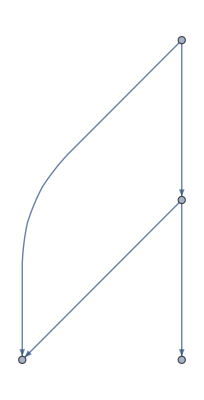
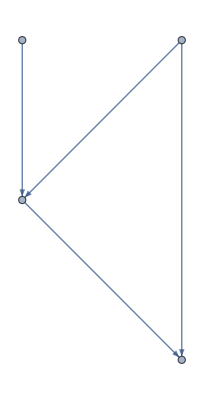

```mathematica
{AdjacencyGraph[ToExpression[StringSplit[SyntMFinder4N[[36;;39]]]]],AdjacencyGraph[ToExpression[StringSplit[SyntMFinder4N[[43;;46]]]]]}
```

```mathematica
SyntMFinder4N//TableForm
```

Import 100 randomized networks:

```mathematica
SetDirectory["/synthetic random networks"]
```

```mathematica
gRandsSynt=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsSynt//Dimensions
```

{100,80,3}

```mathematica
motCombsSynt=EnrichedCombsMFinderRandUpTo3[g2,Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsSynt,{-Graphics-},{7}]//Quiet;
```

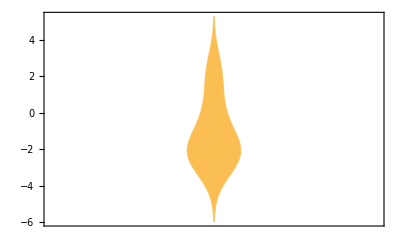

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsSynt[[1]]),PlotRange->All]//Quiet
```

```mathematica
{Select[motCombsSynt[[2]],#[[2]]>0&][[;;,1]],Select[motCombsSynt[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-},{-Graphics-}}

```mathematica
motCombs2ShSynt=EnrichedCombs2ShMFinderRandUpTo3[SimpleGraph@g2,SimpleGraph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsSynt,{-Graphics-},{7}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShSynt[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
{Select[motCombs2ShSynt[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShSynt[[2]],#[[2]]<0&][[;;,1]]}
```

{{},{}}

```mathematica
col=(ColorData["TemperatureMap"][#]&/@Rescale[(#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@Join[motCombsSynt[[1,;;,;;2]],motCombs2ShSynt[[1,;;,;;2]]]])
```

{RGBColor[0.817319, 0.134127, 0.164218],RGBColor[0.40949603301217546, 0.5291066147512493, 0.9473137030137797],RGBColor[0.5466987951185937, 0.6428737362341546, 0.9574572782568591],RGBColor[0.24054783830999446, 0.3701614080506099, 0.9370102155818932],RGBColor[0.9925280126186107, 0.9911781554435481, 0.773493698000499],RGBColor[0.178927, 0.305394, 0.933501],RGBColor[0.6796651461951226, 0.7496788449448423, 0.9687063280069722],RGBColor[0.6018281876394289, 0.6876302606333994, 0.9617972659817181],RGBColor[0.3459154871151503, 0.4740363415464006, 0.9432624068512905],RGBColor[0.43029409433752236, 0.547120850130308, 0.9486389370904273],RGBColor[0.6148634804382574, 0.6982128985607369, 0.9628234519806927],RGBColor[0.6051507835130058, 0.6903276936448074, 0.9620588328999558]}

```mathematica
Grid[{{Item[-Graphics-,Background->col[[1]]],Item[-Graphics-,Background->col[[2]]],Item[-Graphics-,Background->col[[3]]]},
{Item[-Graphics-,Background->col[[4]]],Item[-Graphics-,Background->col[[5]]],Item[-Graphics-,Background->col[[6]]]},
{Item[-Graphics-,Background->col[[7]]],Item[-Graphics-,Background->col[[8]]],Item[-Graphics-,Background->col[[9]]]},
{Item[-Graphics-,Background->col[[10]]],Item[-Graphics-,Background->col[[11]]],Item[-Graphics-,Background->col[[12]]]}},Frame->All]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
BarLegend[{"TemperatureMap",{Min[#],Max[#]}&@((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@Join[motCombsSynt[[1,;;,;;2]],motCombs2ShSynt[[1,;;,;;2]]]//Quiet)}]
```

Synthetic network #2:

```mathematica
g3=Graph[Union[Join[EdgeList[g]/.(Join@@({#[[1,1]]->#[[2,1]],#[[1,2]]->#[[2,2]]}&/@(RandomSample[(Subsets[Range[#-2,#]&/@Table[3x,{x,1,20}],{2}]),120]))),
RandomChoice[#[[1]]]->RandomChoice[#[[2]]]&/@(RandomSample[(Subsets[Range[#-2,#]&/@Table[3x,{x,1,20}],{2}]),20])(*,
RandomChoice[#[[2]]]->RandomChoice[#[[1]]]&/@(Subsets[Range[#-2,#]&/@Table[3x,{x,1,20}],{2}][[101;;]])*)]],EdgeStyle->Black,VertexSize->Tiny];
```

Import the synthetic network:

```mathematica
g3=Graph[DirectedEdge@@@Import["/synt2.txt","Table"][[;;,;;2]],EdgeStyle->Black,VertexSize->Tiny];
```

```mathematica
HighlightGraph[g3,AllSubG[g3,Graph[{1->2,2->3,1->3}]][[1]],GraphLayout->"LayeredDigraphEmbedding"]
```

-Graphics-

```mathematica
EdgeCount[g3]
```

70

```mathematica
VertexCount[g3]
```

46

Detecting network motifs with mathematica:

```mathematica
NetMotFinderAllUp3[g3,1]
```

{{},{},{{-Graphics-,18,11.7005},{-Graphics-,1,5.65774}}}

Detecting network motifs with mFinder:

```mathematica
SyntMFinder23N=Import["/synt2_OUT.txt","Data"];
```

```mathematica
AdjacencyGraph[ToExpression/@StringSplit/@SyntMFinder23N[[38;;40]][[;;,1]]]
```

-Graphics-

```mathematica
SyntMFinder23N//TableForm
```

| 
Summary motif results | 
===================== | 
mfinder Version 1.20 | 
 | 
MOTIF FINDER RESULTS: | 
 | 
Network name: synt1.txt | 
Network type: Directed | 
Num of Nodes: 60 Num of Edges: 140 | 
Num of Nodes with edges: 55 | 
Maximal out degree (out-hub) : 12 | 
Maximal in degree (in-hub) : 10 | 
Roots num: 5 Leaves num: 17 | 
Single Edges num: 138 Mutual Edges num: 1 | 
 | 
Motif size searched  3 | 
Total number of 3-node subgraphs : 720 | 
Number of random networks generated : 100 | 
Random networks generation method: Switches | 
Num of Switches range: 100.0-200.0 | Success switches Ratio:0.674+-0.00
 | 
The following motifs were found: | 
 | 
Criteria taken : Nreal Zscore > 2.00 | 
Pval ignored (due to small number of random networks) | 
Mfactor > 1.10 | 
Uniqueness >= 4 | 
 | 
 | 
 | 
Full list includes 1 motifs | 
MOTIF	NREAL	NRAND		NREAL	NREAL	UNIQ	CREAL | 
ID		STATS		ZSCORE	PVAL	VAL	[MILI] | 
 | 
38	44	27.5+-4.2	3.94	0.000	11	61.11 | 
 | 
0 1 1 | 
0 0 1 | 
0 0 0 | 
 | 
 | 
 | 
 | 
Full list of subgraphs size 3 ids: | 
 | 
( Total num of different subgraphs size 3 is : 13 ) | 
 | 
MOTIF	NREAL	NRAND		NREAL	NREAL	CREAL	UNIQ | 
ID		STATS		ZSCORE	PVAL	[MILI] | 
6	257	273.5+-4.2	-3.94	1.000	356.94	14 | 
 | 
12	233	243.3+-6.4	-1.62	0.930	323.61	11 | 
 | 
14	9	12.1+-1.4	-2.23	1.000	12.50	1 | 
 | 
36	167	184.8+-4.3	-4.11	1.000	231.94	11 | 
 | 
38	44	27.5+-4.2	3.94	0.000	61.11	11 | 
 | 
46	2	0.8+-0.7	1.81	0.140	2.78	1 | 
 | 
74	7	7.6+-0.5	-1.25	0.990	9.72	1 | 
 | 
78	0	0.0+-0.0	888888	1.000	0.00	0 | 
 | 
98	0	2.3+-1.6	-1.40	1.000	0.00	0 | 
 | 
102	1	0.4+-0.5	1.25	0.360	1.39	1 | 
 | 
108	0	0.0+-0.0	888888	1.000	0.00	0 | 
 | 
110	0	0.0+-0.0	888888	1.000	0.00	0 | 
 | 
238	0	0.0+-0.0	888888	1.000	0.00	0 | 
 | 
 | 
 | 
(Application total runtime was:    1.0 seconds.) | 
 | 
(Real network processing runtime was:    0.0 seconds.) | 
 | 
(Single Random network processing runtime was:    0.0 seconds.) |

```mathematica
SyntMFinder24N=Import["/synt24N_OUT.txt","Data"];
```

```mathematica
{AdjacencyGraph[ToExpression[StringSplit[SyntMFinder24N[[36;;39]]]]],AdjacencyGraph[ToExpression[StringSplit[SyntMFinder24N[[43;;46]]]]],AdjacencyGraph[ToExpression[StringSplit[SyntMFinder24N[[50;;53]]]]]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
SyntMFinder24N//TableForm
```

Summary motif results
   =====================
mfinder Version 1.20

MOTIF FINDER RESULTS:

	Network name: synt2.txt
	Network type: Directed
	Num of Nodes: 60 Num of Edges: 70
	Num of Nodes with edges: 46
	Maximal out degree (out-hub) : 5
	Maximal in degree (in-hub) : 3
	Roots num: 11 Leaves num: 12
	Single Edges num: 66 Mutual Edges num: 2

	Motif size searched  4
	Total number of 4-node subgraphs : 247
	Number of random networks generated : 100
	Random networks generation method: Switches (with metropolis)

The following motifs were found:

Criteria taken : Nreal Zscore > 2.00
                 Pval ignored (due to small number of random networks)
                 Mfactor > 1.10
                 Uniqueness >= 4



	Full list includes 3 motifs
MOTIF	NREAL	NRAND		NREAL	NREAL	UNIQ	CREAL
ID		STATS		ZSCORE	PVAL	VAL	[MILI]	

14	12	7.0+-2.0	2.47	0.020	5	48.58

0 1 1 1 
0 0 0 0 
0 0 0 0 
0 0 0 0 

206	12	1.7+-1.2	8.95	0.000	6	48.58

0 1 1 1 
0 0 1 1 
0 0 0 0 
0 0 0 0 

2186	7	3.3+-1.2	3.02	0.000	5	28.34

0 1 0 1 
0 0 0 1 
0 0 0 1 
0 0 0 0 




Full list of subgraphs size 4 ids:

	( Total num of different subgraphs size 4 is : 199 )

MOTIF	NREAL	NRAND		NREAL	NREAL	CREAL	UNIQ
ID		STATS		ZSCORE	PVAL	[MILI]	
14	12	7.0+-2.0	2.47	0.020	48.58	5

28	19	17.7+-3.4	0.37	0.370	76.92	4

30	3	2.8+-1.2	0.17	0.480	12.15	1

74	49	49.4+-9.2	-0.04	0.570	198.38	4

76	34	44.9+-7.4	-1.47	0.970	137.65	4

78	2	12.7+-2.5	-4.35	1.000	8.10	1

90	0	0.7+-1.4	-0.49	1.000	0.00	0

92	0	14.2+-2.7	-5.30	1.000	0.00	0

94	0	0.0+-0.0	888888	1.000	0.00	0

204	0	0.1+-0.3	-0.33	1.000	0.00	0

206	12	1.7+-1.2	8.95	0.000	48.58	6

222	0	0.0+-0.0	888888	1.000	0.00	0

280	9	6.6+-2.6	0.95	0.250	36.44	2

282	3	1.5+-1.3	1.23	0.280	12.15	1

286	0	0.0+-0.0	888888	1.000	0.00	0

328	25	30.7+-6.6	-0.86	0.820	101.21	3

330	0	0.0+-0.0	888888	1.000	0.00	0

332	0	0.2+-0.6	-0.33	1.000	0.00	0

334	0	1.5+-1.3	-1.15	1.000	0.00	0

344	6	5.6+-2.5	0.16	0.490	24.29	4

346	0	0.2+-0.5	-0.32	1.000	0.00	0

348	1	1.6+-1.6	-0.36	0.660	4.05	1

350	0	0.0+-0.0	888888	1.000	0.00	0

390	0	2.4+-1.8	-1.33	1.000	0.00	0

392	29	30.0+-5.2	-0.19	0.550	117.41	3

394	14	9.4+-2.6	1.77	0.050	56.68	3

396	4	2.5+-1.4	1.08	0.240	16.19	2

398	0	1.2+-1.0	-1.26	1.000	0.00	0

404	3	1.2+-1.1	1.72	0.110	12.15	1

406	0	0.0+-0.0	888888	1.000	0.00	0

408	10	6.9+-2.1	1.49	0.100	40.49	3

410	0	0.0+-0.0	888888	1.000	0.00	0

412	0	0.4+-0.6	-0.67	1.000	0.00	0

414	0	0.0+-0.0	888888	1.000	0.00	0

454	0	0.9+-1.0	-0.91	1.000	0.00	0

456	0	0.3+-0.6	-0.48	1.000	0.00	0

458	0	0.0+-0.0	888888	1.000	0.00	0

460	0	0.0+-0.0	888888	1.000	0.00	0

462	3	0.2+-0.5	5.66	0.000	12.15	1

468	0	1.0+-0.8	-1.32	1.000	0.00	0

470	0	0.0+-0.0	888888	1.000	0.00	0

472	0	1.9+-1.2	-1.51	1.000	0.00	0

474	0	0.0+-0.0	888888	1.000	0.00	0

476	0	0.4+-0.6	-0.72	1.000	0.00	0

478	0	0.0+-0.0	888888	1.000	0.00	0

856	0	0.0+-0.0	888888	1.000	0.00	0

858	0	0.0+-0.0	888888	1.000	0.00	0

862	0	0.0+-0.0	888888	1.000	0.00	0

904	0	0.2+-0.4	-0.41	1.000	0.00	0

906	0	2.0+-1.4	-1.40	1.000	0.00	0

908	0	0.0+-0.1	-0.10	1.000	0.00	0

910	0	0.0+-0.0	888888	1.000	0.00	0

922	0	0.0+-0.0	888888	1.000	0.00	0

924	0	0.0+-0.2	-0.16	1.000	0.00	0

926	0	0.0+-0.0	888888	1.000	0.00	0

972	0	0.0+-0.0	888888	1.000	0.00	0

974	0	0.0+-0.0	888888	1.000	0.00	0

990	0	0.0+-0.0	888888	1.000	0.00	0

2184	0	0.9+-0.8	-1.14	1.000	0.00	0

2186	7	3.3+-1.2	3.02	0.000	28.34	5

2190	0	0.5+-0.7	-0.71	1.000	0.00	0

2202	0	0.0+-0.0	888888	1.000	0.00	0

2204	0	1.1+-1.1	-0.98	1.000	0.00	0

2206	0	0.0+-0.0	888888	1.000	0.00	0

2252	0	0.4+-0.7	-0.63	1.000	0.00	0

2254	0	0.8+-0.7	-1.14	1.000	0.00	0

2270	0	0.0+-0.0	888888	1.000	0.00	0

2458	0	0.0+-0.0	888888	1.000	0.00	0

2462	0	0.0+-0.0	888888	1.000	0.00	0

2506	0	0.0+-0.0	888888	1.000	0.00	0

2510	0	0.0+-0.0	888888	1.000	0.00	0

2524	0	0.0+-0.0	888888	1.000	0.00	0

2526	0	0.0+-0.0	888888	1.000	0.00	0

3038	0	0.0+-0.0	888888	1.000	0.00	0

4370	0	0.0+-0.0	888888	1.000	0.00	0

4374	0	0.0+-0.0	888888	1.000	0.00	0

4382	0	0.0+-0.0	888888	1.000	0.00	0

4418	0	0.0+-0.0	888888	1.000	0.00	0

4420	0	0.1+-0.2	-0.23	1.000	0.00	0

4422	1	0.8+-0.4	0.47	0.820	4.05	1

4424	0	0.8+-0.9	-0.84	1.000	0.00	0

4426	0	0.0+-0.0	888888	1.000	0.00	0

4428	0	0.0+-0.0	888888	1.000	0.00	0

4430	0	0.0+-0.0	888888	1.000	0.00	0

4434	0	0.0+-0.0	888888	1.000	0.00	0

4436	0	0.0+-0.0	888888	1.000	0.00	0

4438	0	0.0+-0.0	888888	1.000	0.00	0

4440	0	0.0+-0.0	888888	1.000	0.00	0

4442	0	0.0+-0.0	888888	1.000	0.00	0

4444	0	0.0+-0.0	888888	1.000	0.00	0

4446	0	0.0+-0.0	888888	1.000	0.00	0

4546	0	0.0+-0.0	888888	1.000	0.00	0

4548	0	0.0+-0.0	888888	1.000	0.00	0

4550	0	0.0+-0.0	888888	1.000	0.00	0

4556	0	0.0+-0.0	888888	1.000	0.00	0

4558	0	0.0+-0.0	888888	1.000	0.00	0

4562	0	0.0+-0.0	888888	1.000	0.00	0

4564	0	0.0+-0.0	888888	1.000	0.00	0

4566	0	0.0+-0.0	888888	1.000	0.00	0

4572	0	0.0+-0.0	888888	1.000	0.00	0

4574	0	0.0+-0.0	888888	1.000	0.00	0

4678	1	0.8+-0.9	0.17	0.530	4.05	1

4682	0	0.0+-0.1	-0.10	1.000	0.00	0

4686	0	0.1+-0.2	-0.25	1.000	0.00	0

4692	0	0.5+-0.5	-1.00	1.000	0.00	0

4694	0	0.0+-0.0	888888	1.000	0.00	0

4698	0	0.0+-0.0	888888	1.000	0.00	0

4700	0	0.0+-0.0	888888	1.000	0.00	0

4702	0	0.0+-0.0	888888	1.000	0.00	0

4740	0	0.1+-0.3	-0.27	1.000	0.00	0

4742	0	0.0+-0.0	888888	1.000	0.00	0

4748	0	0.0+-0.0	888888	1.000	0.00	0

4750	0	0.2+-0.4	-0.42	1.000	0.00	0

4758	0	0.0+-0.0	888888	1.000	0.00	0

4764	0	0.0+-0.0	888888	1.000	0.00	0

4766	0	0.0+-0.0	888888	1.000	0.00	0

4812	0	0.0+-0.0	888888	1.000	0.00	0

4814	0	0.0+-0.1	-0.10	1.000	0.00	0

4830	0	0.0+-0.0	888888	1.000	0.00	0

4946	0	0.0+-0.0	888888	1.000	0.00	0

4950	0	0.0+-0.0	888888	1.000	0.00	0

4952	0	0.0+-0.0	888888	1.000	0.00	0

4954	0	0.0+-0.0	888888	1.000	0.00	0

4958	0	0.0+-0.0	888888	1.000	0.00	0

4994	0	0.0+-0.0	888888	1.000	0.00	0

4998	0	0.0+-0.0	888888	1.000	0.00	0

5002	0	0.1+-0.3	-0.29	1.000	0.00	0

5004	0	0.0+-0.0	888888	1.000	0.00	0

5006	0	0.0+-0.0	888888	1.000	0.00	0

5010	0	0.0+-0.0	888888	1.000	0.00	0

5012	0	0.0+-0.0	888888	1.000	0.00	0

5014	0	0.0+-0.0	888888	1.000	0.00	0

5016	0	0.0+-0.0	888888	1.000	0.00	0

5018	0	0.0+-0.0	888888	1.000	0.00	0

5020	0	0.0+-0.0	888888	1.000	0.00	0

5022	0	0.0+-0.0	888888	1.000	0.00	0

5058	0	0.0+-0.0	888888	1.000	0.00	0

5062	0	0.0+-0.0	888888	1.000	0.00	0

5064	0	0.0+-0.0	888888	1.000	0.00	0

5066	0	0.0+-0.0	888888	1.000	0.00	0

5068	0	0.0+-0.0	888888	1.000	0.00	0

5070	0	0.0+-0.0	888888	1.000	0.00	0

5074	0	0.0+-0.0	888888	1.000	0.00	0

5076	0	0.0+-0.0	888888	1.000	0.00	0

5078	0	0.0+-0.0	888888	1.000	0.00	0

5080	0	0.0+-0.0	888888	1.000	0.00	0

5082	0	0.0+-0.0	888888	1.000	0.00	0

5084	0	0.0+-0.0	888888	1.000	0.00	0

5086	0	0.0+-0.0	888888	1.000	0.00	0

6342	0	0.0+-0.0	888888	1.000	0.00	0

6348	0	0.0+-0.0	888888	1.000	0.00	0

6350	0	0.0+-0.0	888888	1.000	0.00	0

6356	0	0.0+-0.0	888888	1.000	0.00	0

6358	0	0.0+-0.0	888888	1.000	0.00	0

6364	0	0.0+-0.0	888888	1.000	0.00	0

6366	0	0.0+-0.0	888888	1.000	0.00	0

6550	0	0.0+-0.0	888888	1.000	0.00	0

6552	0	0.0+-0.0	888888	1.000	0.00	0

6554	0	0.0+-0.0	888888	1.000	0.00	0

6558	0	0.0+-0.0	888888	1.000	0.00	0

6598	0	0.0+-0.0	888888	1.000	0.00	0

6602	0	0.0+-0.0	888888	1.000	0.00	0

6604	0	0.0+-0.0	888888	1.000	0.00	0

6606	0	0.0+-0.0	888888	1.000	0.00	0

6614	0	0.0+-0.0	888888	1.000	0.00	0

6616	0	0.0+-0.0	888888	1.000	0.00	0

6618	0	0.0+-0.0	888888	1.000	0.00	0

6620	0	0.0+-0.0	888888	1.000	0.00	0

6622	0	0.0+-0.0	888888	1.000	0.00	0

6854	0	0.0+-0.0	888888	1.000	0.00	0

6858	0	0.0+-0.0	888888	1.000	0.00	0

6862	0	0.0+-0.0	888888	1.000	0.00	0

6870	0	0.0+-0.0	888888	1.000	0.00	0

6874	0	0.0+-0.0	888888	1.000	0.00	0

6876	0	0.0+-0.0	888888	1.000	0.00	0

6878	0	0.0+-0.0	888888	1.000	0.00	0

7126	0	0.0+-0.0	888888	1.000	0.00	0

7128	0	0.0+-0.0	888888	1.000	0.00	0

7130	0	0.0+-0.0	888888	1.000	0.00	0

7134	0	0.0+-0.0	888888	1.000	0.00	0

13142	0	0.0+-0.0	888888	1.000	0.00	0

13146	0	0.0+-0.0	888888	1.000	0.00	0

13148	0	0.0+-0.0	888888	1.000	0.00	0

13150	0	0.0+-0.0	888888	1.000	0.00	0

13260	0	0.0+-0.0	888888	1.000	0.00	0

13262	0	0.0+-0.0	888888	1.000	0.00	0

13278	0	0.0+-0.0	888888	1.000	0.00	0

14678	0	0.0+-0.0	888888	1.000	0.00	0

14686	0	0.0+-0.0	888888	1.000	0.00	0

14790	0	0.0+-0.0	888888	1.000	0.00	0

14798	0	0.0+-0.0	888888	1.000	0.00	0

14810	0	0.0+-0.0	888888	1.000	0.00	0

14812	0	0.0+-0.0	888888	1.000	0.00	0

14814	0	0.0+-0.0	888888	1.000	0.00	0

15258	0	0.0+-0.0	888888	1.000	0.00	0

15262	0	0.0+-0.0	888888	1.000	0.00	0

15310	0	0.0+-0.0	888888	1.000	0.00	0

15326	0	0.0+-0.0	888888	1.000	0.00	0

31710	0	0.0+-0.0	888888	1.000	0.00	0



 (Application total runtime was:   10.0 seconds.)

 (Real network processing runtime was:    0.0 seconds.)

 (Single Random network processing runtime was:    0.1 seconds.)

Import 100 randomized networks:

```mathematica
SetDirectory["/synthetic2 random networks"]
```

```mathematica
gRandsSynt2=Import[#,"Data"]&/@FileNames[];
```

```mathematica
gRandsSynt2//Dimensions
```

{100,70,3}

```mathematica
motCombsSynt2=EnrichedCombsMFinderRandUpTo3[g3,Graph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsSynt2,{-Graphics-},{7}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombsSynt2[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
{Select[motCombsSynt2[[2]],#[[2]]>0&][[;;,1]],Select[motCombsSynt2[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-,-Graphics-},{}}

```mathematica
motCombsSynt2[[2;;]]
```

{{{-Graphics-,2.74374,0.025},{-Graphics-,2.52133,0.0333333}},, | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  | -Graphics- | -Graphics-
-Graphics- |  |  | -Graphics-}

```mathematica
motCombs2ShSynt2=EnrichedCombs2ShMFinderRandUpTo3[SimpleGraph@g3,SimpleGraph[DirectedEdge@@@#[[;;,;;2]]]&/@gRandsSynt2,{-Graphics-},{7}]//Quiet;
```

```mathematica
DistributionChart[((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@motCombs2ShSynt2[[1]]),PlotRange->All]//Quiet
```

-Graphics-

```mathematica
{Select[motCombs2ShSynt2[[2]],#[[2]]>0&][[;;,1]],Select[motCombs2ShSynt2[[2]],#[[2]]<0&][[;;,1]]}
```

{{-Graphics-},{-Graphics-}}

```mathematica
motCombs2ShSynt2[[3;;]]
```

{, | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- |  | -Graphics- | -Graphics-
-Graphics- |  |  | -Graphics-}

```mathematica
col2=(ColorData["TemperatureMap"][#]&/@Rescale[(#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@Join[motCombsSynt2[[1,;;,;;2]],motCombs2ShSynt2[[1,;;,;;2]]]])
```

{RGBColor[0.178927, 0.305394, 0.933501],RGBColor[0.5121973238041619, 0.6148638875475285, 0.9547411960519334],RGBColor[0.1925703991787642, 0.31973407757835154, 0.9342779713996303],RGBColor[0.9942725464553674, 0.9901578809394401, 0.617980211291893],RGBColor[0.9934413952893059, 0.9883801326375077, 0.5275145361365071],RGBColor[0.276269610119129, 0.40770725511315686, 0.9390445176407978],RGBColor[0.3449239181172228, 0.47317749431810274, 0.9431992249515526],RGBColor[0.35345651440624176, 0.4805680003628919, 0.9437429144420102],RGBColor[0.4040569044940093, 0.5243955150073619, 0.9469671265542347],RGBColor[0.817319, 0.134127, 0.164218],RGBColor[0.47067571713187867, 0.5811547767239048, 0.9514724630760344],RGBColor[0.48515928406596937, 0.5929131888382544, 0.9526126625201399]}

```mathematica
Grid[{{Item[-Graphics-,Background->col2[[1]]],Item[-Graphics-,Background->col2[[2]]],Item[-Graphics-,Background->col2[[3]]]},
{Item[-Graphics-,Background->col2[[4]]],Item[-Graphics-,Background->col2[[5]]],Item[-Graphics-,Background->col2[[6]]]},
{Item[-Graphics-,Background->col2[[7]]],Item[-Graphics-,Background->col2[[8]]],Item[-Graphics-,Background->col2[[9]]]},
{Item[-Graphics-,Background->col2[[10]]],Item[-Graphics-,Background->col2[[11]]],Item[-Graphics-,Background->col2[[12]]]}},Frame->All]
```

-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
BarLegend[{"TemperatureMap",{Min[#],Max[#]}&@((#[[1]]-Mean[#[[2]]])/StandardDeviation[#[[2]]]&/@Join[motCombsSynt2[[1,;;,;;2]],motCombs2ShSynt2[[1,;;,;;2]]]//Quiet)}]
```